# Calculation of thermoradiative diode efficiency with Urbach tail

In this file we calculate ...

```mathematica
(* defining some constants *)
constants ={hbar ->  1.05457173 10^-34,
m0 ->  9.10938291 10^-31,
kB ->  1.3806488 10^-23,
echarge ->  1.60217657 10^-19,
eps0 ->  8.854188 10^-12,
clight  -> 299792458,
Tsun ->  6000 1.3806488 10^-23/(1.60217657 10^-19),
Tcell ->  300 1.3806488 10^-23/(1.60217657 10^-19),
onesun ->  π/46266,
prefac->(2 π (1.60217657 10^-19)^4)/(299792458^2(2 Pi 1.05457173 10^-34)^3),
sigma->5.670374419 10^-8(1.3806488 10^-23)^-4(1.60217657 10^-19)^4};
```

```mathematica
NIntegrate[(onesun/π prefac)/(Exp[en / Tsun]-1)en^2/.constants,{en,1.42,10}]
```

467.268

0.025852

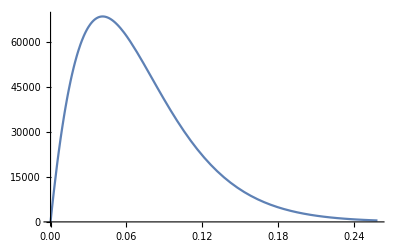

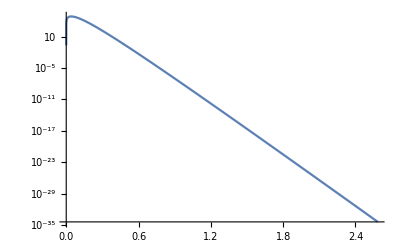

```mathematica
(* illustrating the frequency dependence of the photon flux *)
Tcell /.constants
Plot[prefac/(Exp[en / Tcell]-1)en^2/.constants,{en,0,10 Tcell/.constants}](* photons per m^2 and eV *)
LogPlot[prefac/(Exp[en / Tcell]-1)en^2/.constants,{en,0,100 Tcell/.constants}]
```

## Sharp band gap

```mathematica
(* photon flux in Boltzmann approximation *)
Integrate[Exp[-en/T] en^2,{en,Eg,∞},Assumptions->Eg>0&&T>0]
(* energy flux in Boltzmann approximation *)
Integrate[(Exp[-en/T] en^2)en(* number of photons per energy x energy of each photon *),{en,Eg,∞},Assumptions->Eg>0&&T>0]
```

ⅇ^(-Eg/T) T (Eg^2+2 Eg T+2 T^2)

ⅇ^(-Eg/T) T (Eg^3+3 Eg^2 T+6 Eg T^2+6 T^3)

```mathematica
(* intensity per meV *)
prefac 10^-3 10^-4(Exp[-en/Tcell] en^2)en/.en-> 0.3 /.constants
```

3.90119×10^-6

```mathematica
absorptivitySharp[en_,Eg_]:=HeavisideTheta[en-Eg];
(* emitted photon flux with a sharp band gap and Bose Einstein distribution *)
NemEGPrecise[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ]:=NemEGPrecise[Eg,T,mu]=NIntegrate[1/(Exp[(en-mu) / T]-1)en^2/.constants,{en,Eg,∞}];
EnemEGPrecise[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ]:=EnemEGPrecise[Eg,T,mu]=NIntegrate[1/(Exp[(en-mu) / T]-1)en^3/.constants,{en,Eg,∞}];
(* emitted photon flux with a sharp band gap and Boltzmann distribution *)
NemEGBoltzmann[Eg_,T_,mu_]:=ⅇ^(-(Eg-mu)/T) T (Eg^2+2 Eg T+2 T^2);
emissionEnergyEGBoltzmann[Eg_,T_,mu_]:=ⅇ^(-(Eg-mu)/T) T (Eg^3+3 Eg^2 T+6 Eg T^2+6 T^3);
```

```mathematica
emissionEnergyEGBoltzmann[clight hbar 2 Pi/echarge/12 10^6,Tcell 290/300,0]prefac-emissionEnergyEGBoltzmann[clight hbar 2 Pi/echarge/8 10^6,Tcell 290/300,0]prefac /.constants
```

101.368

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.0259823}. NIntegrate obtained 0.0000354226 and 4.78024×10^-9 for the integral and error estimates.

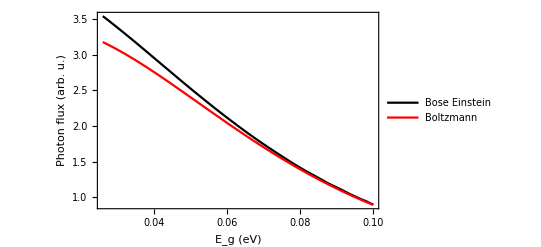

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.0259823}. NIntegrate obtained 0.0000121166 and 1.28691×10^-9 for the integral and error estimates.

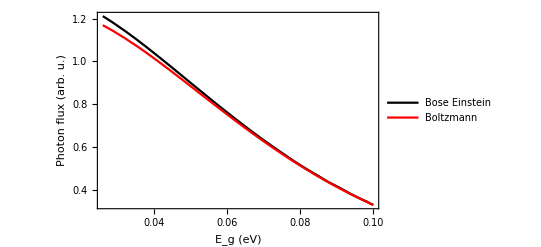

```mathematica
(* comparing photon fluxes in Boltzmann approximation to the precise result for different band gaps *)
Plot[{100000 NemEGPrecise[Eg,Tcell/.constants,0],100000 NemEGBoltzmann[Eg,Tcell/.constants,0]}(* the 2 functions that are plotted in a list *),{Eg,Tcell/.constants,0.1}(* x-axis variable plus lower and upper bound of the x-axis *),PlotStyle->{Black,Red} (* colours of the lines *),Frame->True (* to make a frame around the plot *),LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black}(* Font of the labels *),FrameLabel->{{"Photon flux (arb. u.)","right axis"} (* left and right labels *),{"E_g (eV)","top axis"} (* bottom and top labels *)},PlotLegends->{"Bose Einstein", "Boltzmann"},PerformanceGoal->"Speed" (* in case you have a numerically hard problem, otherwise no need. Speeds up the calculation by sacrificing accuracy *)]
(* reverse bias to illustrate how Boltzmann approximation improves *)
Plot[{100000 NemEGPrecise[Eg,Tcell/.constants,-Tcell/.constants],100000 NemEGBoltzmann[Eg,Tcell/.constants,-Tcell/.constants]}(* the 2 functions that are plotted in a list *),{Eg,Tcell/.constants,0.1}(* x-axis variable plus lower and upper bound of the x-axis *),PlotStyle->{Black,Red} (* colours of the lines *),Frame->True (* to make a frame around the plot *),LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black}(* Font of the labels *),FrameLabel->{{"Photon flux (arb. u.)","right axis"} (* left and right labels *),{"E_g (eV)","top axis"} (* bottom and top labels *)},PlotLegends->{"Bose Einstein", "Boltzmann"},PerformanceGoal->"Speed" (* in case you have a numerically hard problem, otherwise no need. Speeds up the calculation by sacrificing accuracy *)]
```

```mathematica
(* emitted flux - absorbed flux *)
shortCircuitCurrentTRD[Eg_,Ttrd_,Tenv_]:= NemEGBoltzmann[Eg,Ttrd,0]-NemEGBoltzmann[Eg,Tenv,0];
```

General::munfl: Exp[-119880.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-167832.] is too small to represent as a normalized machine number; precision may be lost.

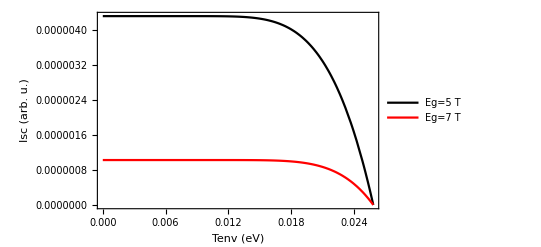

```mathematica
(* short circuit current for different band gaps as a function of temperature *)
Plot[{shortCircuitCurrentTRD[5 Tcell/.constants,Tcell/.constants,Tenv],shortCircuitCurrentTRD[7 Tcell/.constants,Tcell/.constants,Tenv]},{Tenv,0,Tcell/.constants},PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Isc (arb. u.)",""},{"Tenv (eV)",""}},PlotLegends->{"Eg=5 T", "Eg=7 T"},PerformanceGoal->"Speed"]
```

```mathematica
currentTRD[Eg_,Ttrd_,Tenv_,voltage_]:=NemEGBoltzmann[Eg,Ttrd,voltage]-NemEGBoltzmann[Eg,Tenv,0];
emissionEnergyTRD[Eg_,Ttrd_,Tenv_,voltage_]:=emissionEnergyEGBoltzmann[Eg,Ttrd,voltage]-emissionEnergyEGBoltzmann[Eg,Tenv,0]
powerTRD[Eg_,Ttrd_,Tenv_,voltage_]:=-currentTRD[Eg,Ttrd,Tenv,voltage]voltage;
efficiencyTRD[Eg_,Ttrd_,Tenv_,voltage_]:=HeavisideTheta[powerTRD[Eg,Ttrd,Tenv,voltage]](* making sure that only positive power results in an efficiency*)powerTRD[Eg,Ttrd,Tenv,voltage]/(powerTRD[Eg,Ttrd,Tenv,voltage]+emissionEnergyTRD[Eg,Ttrd,Tenv,voltage]);
```

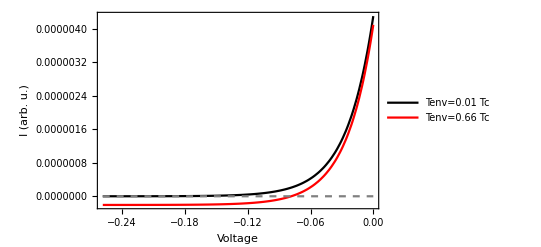

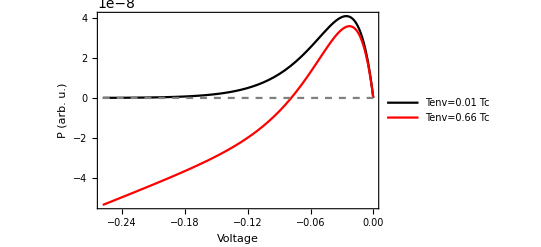

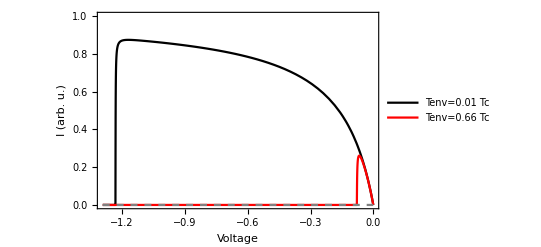

```mathematica
Plot[{currentTRD[5 Tcell/.constants,Tcell/.constants,Tcell/100/.constants,voltage],currentTRD[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,voltage],0},{voltage,-10 Tcell/.constants,0},PlotStyle->{Black,Red,{Gray,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (arb. u.)",""},{"Voltage",""}},PlotLegends->{"Tenv=0.01 Tc", "Tenv=0.66 Tc"},PlotRange->All]
Plot[{powerTRD[5 Tcell/.constants,Tcell/.constants,Tcell/100/.constants,voltage],powerTRD[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,voltage],0},{voltage,-10 Tcell/.constants,0},PlotStyle->{Black,Red,{Gray,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (arb. u.)",""},{"Voltage",""}},PlotLegends->{"Tenv=0.01 Tc", "Tenv=0.66 Tc"},PlotRange->All]
Plot[{efficiencyTRD[5 Tcell/.constants,Tcell/.constants,Tcell/10/.constants,voltage],efficiencyTRD[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,voltage],0},{voltage,-50 Tcell/.constants,0},PlotStyle->{Black,Red,{Gray,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (arb. u.)",""},{"Voltage",""}},PlotLegends->{"Tenv=0.01 Tc", "Tenv=0.66 Tc"},PlotRange->{0,1}]
```

### Nonradiative I-V curve, ideality factor 1

```mathematica
currentTRDNR[Eg_,Ttrd_,Tenv_,voltage_,eta_]:=prefac(NemEGBoltzmann[Eg,Ttrd,voltage]-NemEGBoltzmann[Eg,Tenv,0]+(1-1/eta)(NemEGBoltzmann[Eg,Ttrd,0]-NemEGBoltzmann[Eg,Ttrd,voltage]));
powerTRDNR[Eg_,Ttrd_,Tenv_,voltage_,eta_]:=-currentTRDNR[Eg,Ttrd,Tenv,voltage,eta]voltage;
```

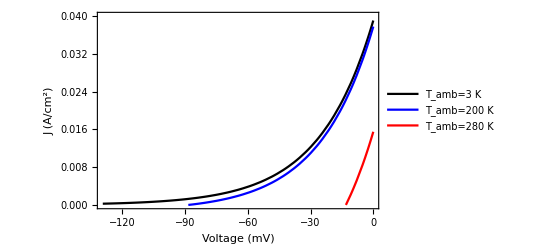

```mathematica
Plot[{10^-4 currentTRDNR[0.15,Tcell/.constants,Tcell/100/.constants,voltage/1000,1]/.constants,10^-4 currentTRDNR[0.15,Tcell/.constants,Tcell/1.5/.constants,voltage/1000,1]/.constants,10^-4 currentTRDNR[0.15,Tcell/.constants,Tcell/300 280/.constants,voltage/1000,1]/.constants},{voltage,-5000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"J (A/cm^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotRange->{0,0.04},PlotLegends->Placed[LineLegend[{"T_amb=3 K","T_amb=200 K","T_amb=280 K"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.2,0.75}]]
```

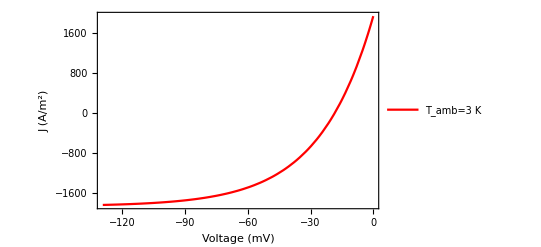

```mathematica
Plot[{currentTRDNR[0.05,Tcell/.constants,250 Tcell/300/.constants,voltage/1000,1]/.constants},{voltage,-5000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"J (A/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotRange->All,PlotLegends->Placed[LineLegend[{"T_amb=3 K","T_amb=200 K","T_amb=280 K"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.2,0.75}]]
```

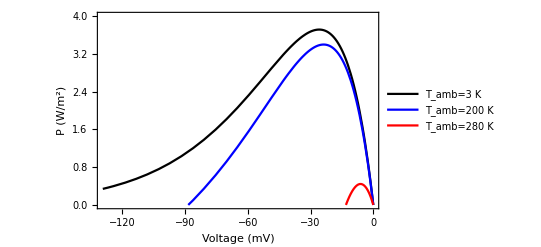

```mathematica
Plot[{-currentTRDNR[0.15,Tcell/.constants,Tcell/100/.constants,voltage/1000,1]voltage/1000/.constants,-currentTRDNR[0.15,Tcell/.constants,Tcell/1.5/.constants,voltage/1000,1]voltage/1000/.constants,-currentTRDNR[0.15,Tcell/.constants,Tcell/300 280/.constants,voltage/1000,1]voltage/1000/.constants},{voltage,-5000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotRange->{0,4},PlotLegends->Placed[LineLegend[{"T_amb=3 K","T_amb=200 K","T_amb=280 K"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.2,0.75}]]
```

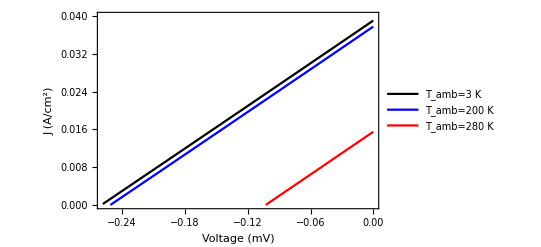

```mathematica
(* Eg_,Ttrd_, Tenv_,impactRate_,thickness_,Eu_,absAboveBandgap_,voltage_ *)
Plot[{10^-4 currentTRDNR[0.15,Tcell/.constants,Tcell/100/.constants,voltage/1000,0.01]/.constants,10^-4 currentTRDNR[0.15,Tcell/.constants,Tcell/1.5/.constants,voltage/1000,0.01]/.constants,10^-4 currentTRDNR[0.15,Tcell/.constants,Tcell/300 280/.constants,voltage/1000,0.01]/.constants},{voltage,-10 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"J (A/cm^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotRange->{0,0.04},PlotLegends->Placed[LineLegend[{"T_amb=3 K","T_amb=200 K","T_amb=280 K"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.2,0.75}]]
```

```mathematica
hbar/echarge clight/10.6 10^6/.constants
currentTRDNR[2 Pi hbar/echarge clight/10.6 10^6,Tcell/.constants,Tcell/100/.constants,0/1000,1]/.constants
```

0.0186158

934.822

## I-V curve with Urbach tail

### Bose Einstein distribution Numerical

```mathematica
(*d (* cm *) absAboveBG (1/cm) = optical thickness (dimensionless) *)
```

```mathematica
thetacr[nrefr_] := ArcSin[1/nrefr];
(* absorption coefficient with Urbach tail *)
absCoeffUrbachSimple[en_,Eg_,Eu_(* urbach energy*),opticalThickness_]:= HeavisideTheta[en-Eg]opticalThickness+HeavisideTheta[Eg-en]opticalThickness Exp[(en-Eg)/Eu];
(* absorptivity for a diode with thickness d and a perfect mirror at the back and a perfect anti-reflection coating at the front *)
absorptivityUrbachSimple[en_,Eg_,Eu_,opticalThickness_,theta_]:= 1-Exp[(-2absCoeffUrbachSimple[en,Eg,Eu,opticalThickness])/Cos[theta]];
(* emitted/absorbed photon flux with Urbach tail and Bose Einstein distribution, neglecting angular dependence *)
NemUrbachSimpleBose[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,nrefr_?NumericQ]:=NIntegrate[absorptivityUrbachSimple[en,Eg,Eu,opticalThickness,0]/(Exp[(en-mu) / T]-1)en^2/.constants,{en,0,∞}];
emissionEnergyUrbachSimpleBose[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,nrefr_?NumericQ]:=NIntegrate[absorptivityUrbachSimple[en,Eg,Eu,opticalThickness,0]/(Exp[(en-mu) / T]-1)en^3/.constants,{en,0,∞}];
```

```mathematica
Integrate[Sin[theta]Cos[theta],{theta,0,Pi/2}]
```

1/2

```mathematica
(* emitted/absorbed photon flux with Urbach tail and Bose Einstein distribution, neglecting angular dependence *)
NemUrbachBose[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,nrefr_?NumericQ]:=NIntegrate[(2 nrefr^2 absorptivityUrbachSimple[en,Eg,Eu,opticalThickness,theta])/(Exp[(en-mu) / T]-1)en^2 Sin[theta]Cos[theta]/.constants,{theta,0,thetacr[nrefr]},{en,0,∞}];
emissionEnergyUrbachBose[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,nrefr_?NumericQ]:=NIntegrate[(2 nrefr^2 absorptivityUrbachSimple[en,Eg,Eu,opticalThickness,theta])/(Exp[(en-mu) / T]-1)en^3 Sin[theta]Cos[theta]/.constants,{theta,0,thetacr[nrefr]},{en,0,∞}];
```

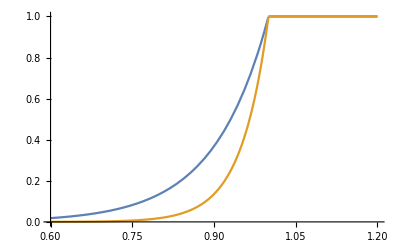

```mathematica
(* just for illustration, smaller urbach Energy gives sharper tail *)
Plot[{absCoeffUrbachSimple[en,1,0.1,1],absCoeffUrbachSimple[en,1,0.05,1]},{en,0.6,1.2}]
```

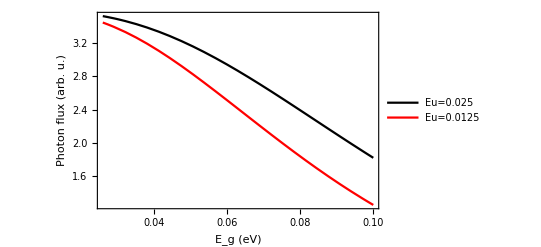

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 3.74335×10^-6 and 1.74908×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.153174}. NIntegrate obtained 1.85966×10^-6 and 8.78309×10^-9 for the integral and error estimates.

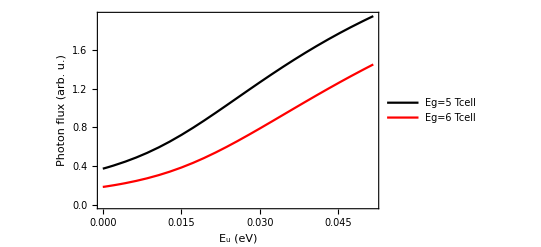

```mathematica
Plot[{100000 NemUrbachSimpleBose[Eg,Tcell/.constants,0,Tcell/.constants,1],100000 NemUrbachSimpleBose[Eg,Tcell/.constants,0,Tcell/2/.constants,1]},{Eg,Tcell/.constants,0.1}(* x-axis variable plus lower and upper bound of the x-axis *),PlotStyle->{Black,Red} (* colours of the lines *),Frame->True (* to make a frame around the plot *),LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black}(* Font of the labels *),FrameLabel->{{"Photon flux (arb. u.)","right axis"} (* left and right labels *),{"E_g (eV)","top axis"} (* bottom and top labels *)},PlotLegends->{"Eu=0.025", "Eu=0.0125"},PerformanceGoal->"Speed" (* in case you have a numerically hard problem, otherwise no need. Speeds up the calculation by sacrificing accuracy *)]
Plot[{100000 NemUrbachSimpleBose[5 Tcell/.constants,Tcell/.constants,0,Eu,1],100000 NemUrbachSimpleBose[6 Tcell/.constants,Tcell/.constants,0,Eu,1]},{Eu,0,2 Tcell/.constants}(* x-axis variable plus lower and upper bound of the x-axis *),PlotStyle->{Black,Red} (* colours of the lines *),Frame->True (* to make a frame around the plot *),LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black}(* Font of the labels *),FrameLabel->{{"Photon flux (arb. u.)","right axis"} (* left and right labels *),{"E_u (eV)","top axis"} (* bottom and top labels *)},PlotLegends->{"Eg=5 Tcell", "Eg=6 Tcell"},PerformanceGoal->"Speed" (* in case you have a numerically hard problem, otherwise no need. Speeds up the calculation by sacrificing accuracy *)]
```

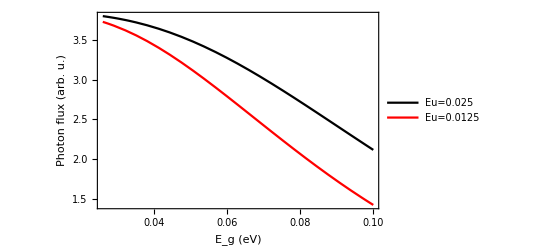

```mathematica
Plot[{100000 NemUrbachBose[Eg,Tcell/.constants,0,Tcell/.constants,1,1.1],100000 NemUrbachBose[Eg,Tcell/.constants,0,Tcell/2/.constants,1,1.1]},{Eg,Tcell/.constants,0.1}(* x-axis variable plus lower and upper bound of the x-axis *),PlotStyle->{Black,Red} (* colours of the lines *),Frame->True (* to make a frame around the plot *),LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black}(* Font of the labels *),FrameLabel->{{"Photon flux (arb. u.)","right axis"} (* left and right labels *),{"E_g (eV)","top axis"} (* bottom and top labels *)},PlotLegends->{"Eu=0.025", "Eu=0.0125"},PerformanceGoal->"Speed" (* in case you have a numerically hard problem, otherwise no need. Speeds up the calculation by sacrificing accuracy *)]
```

```mathematica
currentTRDUrbachBoseSimple[Eg_?NumericQ,Ttrd_?NumericQ,Tenv_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,voltage_?NumericQ]:=NemUrbachSimpleBose[Eg,Ttrd,voltage,Eu,opticalThickness]-NemUrbachSimpleBose[Eg,Tenv,0,Eu,opticalThickness];
emissionEnergyTRDUrbachBoseSimple[Eg_?NumericQ,Ttrd_?NumericQ,Tenv_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,voltage_?NumericQ]:=emissionEnergyUrbachSimpleBose[Eg,Ttrd,voltage,Eu,opticalThickness]-emissionEnergyUrbachSimpleBose[Eg,Tenv,0,Eu,opticalThickness];
powerTRDUBS[Eg_?NumericQ,Ttrd_?NumericQ,Tenv_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,voltage_?NumericQ]:=-currentTRDUrbachBoseSimple[Eg,Ttrd,Tenv,Eu,opticalThickness,voltage]voltage;
efficiencyTRDUBS[Eg_?NumericQ,Ttrd_?NumericQ,Tenv_?NumericQ,Eu_?NumericQ,opticalThickness_?NumericQ,voltage_?NumericQ]:=HeavisideTheta[powerTRDUBS[Eg,Ttrd,Tenv,Eu,opticalThickness,voltage]](* making sure that only positive power results in an efficiency*)powerTRDUBS[Eg,Ttrd,Tenv,Eu,opticalThickness,voltage]/(powerTRDUBS[Eg,Ttrd,Tenv,Eu,opticalThickness,voltage]+emissionEnergyTRDUrbachBoseSimple[Eg,Ttrd,Tenv,Eu,opticalThickness,voltage]);
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.25801}. NIntegrate obtained 8.69298×10^-8 and 2.38826×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.25801}. NIntegrate obtained 9.60194×10^-9 and 3.35629×10^-13 for the integral and error estimates.

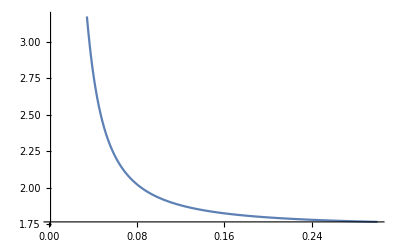

```mathematica
(* understanding why lower temperature emission increases with  more with increasing urbach tail *)
Plot[{NemUrbachSimpleBose[10 Tcell/.constants,Tcell/.constants,0,Eu,1]/NemUrbachSimpleBose[10 Tcell/.constants,Tcell/1.2/.constants,0,Eu,1]},{Eu,0.001,0.3}]
```

```mathematica
sigma T^4/.T->300/.constants
```

459.3

```mathematica
powerTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,0.01,1,0.1]
Plot[{prefac powerTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,0.01,1,voltage]/.constants,prefac powerTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,0.02,1,voltage]/.constants,0},{voltage,-4 Tcell/.constants,0},PlotStyle->{Black,Red,{Gray,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage","Td=300K, Tenv=200K"}},PlotLegends->{"Eu=0.01eV", "Eu=0.02eV"},PlotRange->{0,10},PerformanceGoal->"Speed"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.0987312}. NIntegrate obtained 0.000331621 and 0.00009986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 4.05904×10^-7 and 5.95493×10^-12 for the integral and error estimates.

-0.0000331215

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 1.04609×10^-7 and 1.02929×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 4.05904×10^-7 and 5.95493×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 1.59423×10^-7 and 6.32931×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

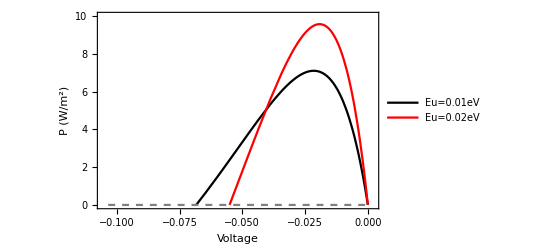

### Back to general

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 1.4157×10^-8 and 1.3928×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 2.15699×10^-8 and 8.56401×10^-14 for the integral and error estimates.

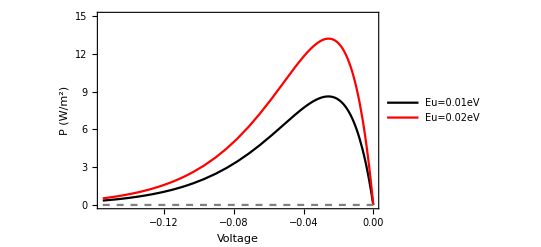

```mathematica
Plot[{prefac powerTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/10/.constants,0.01,1,voltage]/.constants,prefac powerTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/10/.constants,0.02,1,voltage]/.constants,0},{voltage,-6 Tcell/.constants,0},PlotStyle->{Black,Red,{Gray,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage","Td=300K, Tenv=30K"}},PlotLegends->{"Eu=0.01eV", "Eu=0.02eV"},PlotRange->{0,15},PerformanceGoal->"Speed"]
```

```mathematica
efficiencyTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,0.01,1,-0.05]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {1.00006}. NIntegrate obtained -0.00368874 and 0.00184732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 8.26199×10^-7 and 8.13676×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 4.05904×10^-7 and 5.95493×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.231863

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 2.84407×10^-7 and 2.79901×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 4.05904×10^-7 and 5.95493×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 2.84407×10^-7 and 2.79901×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

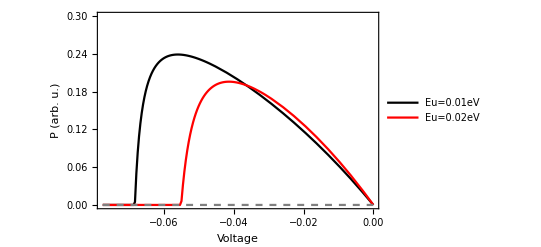

```mathematica
Plot[{efficiencyTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,0.01,1,voltage],efficiencyTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/1.5/.constants,0.02,1,voltage],0},{voltage,-3 Tcell/.constants,0},PlotStyle->{Black,Red,{Gray,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (arb. u.)",""},{"Voltage","Td=300K, Tenv=200K"}},PlotLegends->{"Eu=0.01eV", "Eu=0.02eV"},PlotRange->{0,0.3},PerformanceGoal->"Speed"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.127773}. NIntegrate obtained 1.17786×10^-14 and 1.15879×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

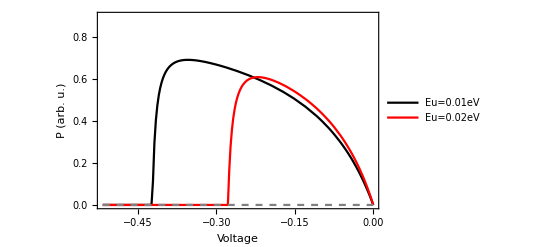

```mathematica
Plot[{efficiencyTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/10/.constants,0.01,1,voltage],efficiencyTRDUBS[5 Tcell/.constants,Tcell/.constants,Tcell/10/.constants,0.02,1,voltage],0},{voltage,-20 Tcell/.constants,0},PlotStyle->{Black,Red,{Gray,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (arb. u.)",""},{"Voltage","Td=300K, Tenv=30K"}},PlotLegends->{"Eu=0.01eV", "Eu=0.02eV"},PlotRange->{0,0.9},PerformanceGoal->"Speed"]
```

### Analysing PolyLog Urbach tail

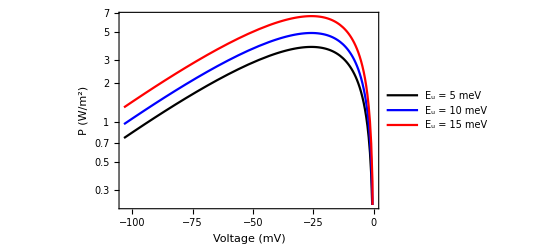

```mathematica
(* Eg_,Ttrd_, Tenv_,impactRate_,thickness_,Eu_,absAboveBandgap_,voltage_ *)
LogPlot[{10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-3,0.005,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-3,0.01,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-3,0.015,10^4,voltage/1000]/.constants},{voltage,-4000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"E_u = 5 meV","E_u = 10 meV","E_u = 15 meV"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.65,0.35}]]
```

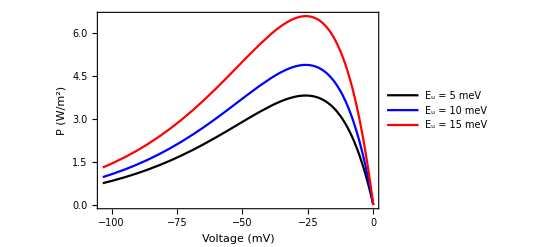

```mathematica
(* Eg_,Ttrd_, Tenv_,impactRate_,thickness_,Eu_,absAboveBandgap_,voltage_ *)
Plot[{10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-3,0.005,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-3,0.01,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-3,0.015,10^4,voltage/1000]/.constants},{voltage,-4000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"E_u = 5 meV","E_u = 10 meV","E_u = 15 meV"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.25,0.75}]]
```

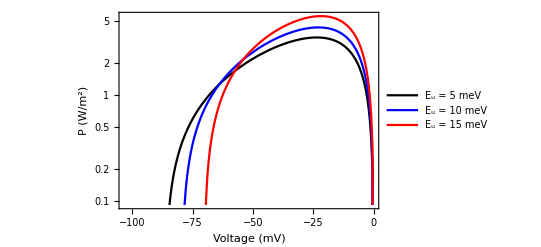

```mathematica
LogPlot[{10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/1.5/.constants,0,10^-3,0.005,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/1.5/.constants,0,10^-3,0.01,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/1.5/.constants,0,10^-3,0.015,10^4,voltage/1000]/.constants},{voltage,-4000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"E_u = 5 meV","E_u = 10 meV","E_u = 15 meV"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.7,0.35}]]
```

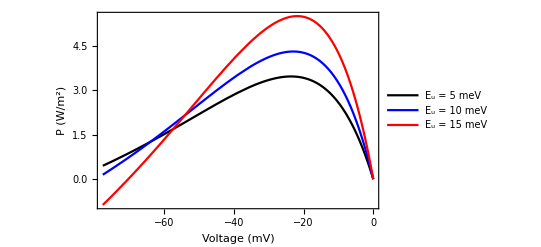

```mathematica
Plot[{10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/1.5/.constants,0,10^-3,0.005,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/1.5/.constants,0,10^-3,0.01,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/1.5/.constants,0,10^-3,0.015,10^4,voltage/1000]/.constants},{voltage,-3000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"E_u = 5 meV","E_u = 10 meV","E_u = 15 meV"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.2,0.75}]]
```

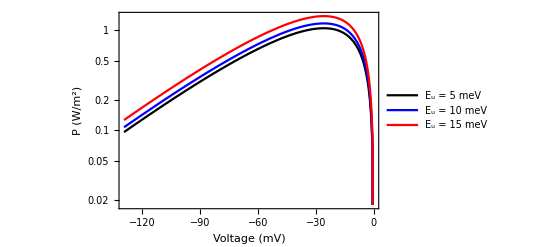

```mathematica
LogPlot[{10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-4,0.005,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-4,0.01,10^4,voltage/1000]/.constants,10^4 powerTRDAugerGuerra[0.15,Tcell/.constants,Tcell/100/.constants,0,10^-4,0.015,10^4,voltage/1000]/.constants},{voltage,-5000 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"E_u = 5 meV","E_u = 10 meV","E_u = 15 meV"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.7,0.35}]]
```

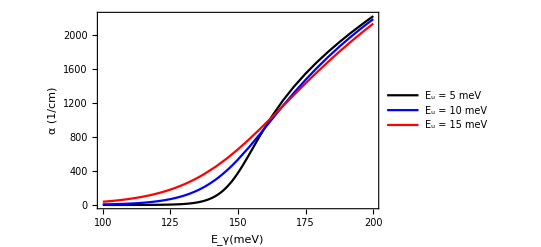

```mathematica
Plot[{absGuerra[en/1000,0.15,0.005,10^4]/.constants,absGuerra[en/1000,0.15,0.01,10^4]/.constants,absGuerra[en/1000,0.15,0.015,10^4]/.constants},{en,100,200},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"α (1/cm)",""},{"E_γ(meV)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"E_u = 5 meV","E_u = 10 meV","E_u = 15 meV"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.25,0.75}]]
```

### Analysing InAs with Auger recombination

(* Auger coefficient, dependence on effective mass, band gap and temperature, taken from Aytac2015*)
(me/m0(T/Eg)^(3/2)Exp[(-(1+2mratio)Eg)/((1+mratio) T)])/((1+mratio)^(1/2)(1+2 mratio)ni^2);
mratio = me/mh;(* 0.023/0.41 ~ 0.05 for InAs *)

```mathematica
((16.5 8 (2 Pi)^(5/2)echarge^4 eps0)/(2 Pi hbar)^3)^-1/.constants
```

3.81728×10^-18

```mathematica
inversetauAuger[Tdf_]:=(16.5 eps0 8 (2 Pi)^(5/2)echarge^4 me (Tdf/0.354)^(3/2)F^2)/((2 Pi hbar)^3 epsinf^2)Exp[(-(1+2 mratio)0.35)/((1+mratio)  Tdf)]/((1+mratio)^(1/2)(1+2 mratio)ni^2)/.constants/.mratio->0.023/0.41/.me->0.023/.ni->10^15/.F->0.1/.epsinf->10;
```

```mathematica
inversetauAuger[0.026]
```

7.31279×10^-27

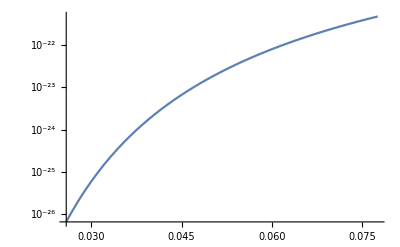

```mathematica
LogPlot[inversetauAuger[T],{T,Tcell/.constants,3 Tcell/.constants}]
```

```mathematica
(* Approximation for the Urbach tail by Guerra et al. 2019*)
absGuerra[omega_,Eg_,Eu_,alpha0_]:=-alpha0/2 Sqrt[π Eu]PolyLog[1/2,-Exp[(omega-Eg)/Eu]];
absorptivityGuerra[omega_,Eg_,Eu_,alpha0_,thickness_]:=1-Exp[-2 absGuerra[omega,Eg,Eu,alpha0 ]thickness];
NemGuerra[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ,thickness_?NumericQ,Eu_?NumericQ,absAboveBandgap_?NumericQ]:=NemGuerra[Eg,T,mu,thickness,Eu,absAboveBandgap]=NIntegrate[Re[absorptivityGuerra[en,Eg,Eu,absAboveBandgap,thickness]]/(Exp[(en-mu) / T]-1)en^2/.constants,{en,Eg-10Eu,∞}];
currentTRDAugerGuerra[Eg_?NumericQ,Ttrd_?NumericQ,Tenv_?NumericQ,impactRate_?NumericQ,thickness_,Eu_?NumericQ,absAboveBandgap_?NumericQ,voltage_?NumericQ]:=10^-4 prefac/echarge NemGuerra[Eg,Ttrd,voltage,thickness,Eu,absAboveBandgap]-10^-4(*to convert into cm^2*)prefac/echarge NemGuerra[Eg,Tenv,0,thickness,Eu,absAboveBandgap]-(Exp[voltage/(2 Ttrd)]-Exp[3 voltage/(2Ttrd)])impactRate thickness;
powerTRDAugerGuerra[Eg_,Ttrd_, Tenv_,impactRate_,thickness_,Eu_,absAboveBandgap_,voltage_]:= -currentTRDAugerGuerra[Eg,Ttrd,Tenv,impactRate,thickness,Eu,absAboveBandgap,voltage]voltage echarge;
```

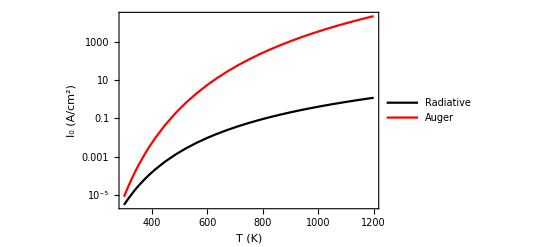

```mathematica
LogPlot[{10^-4 prefac  NemGuerra[0.354,T/300 Tcell,0,10^-5,0.005,1.5 10^4]/.constants,10^-26 nintrInAs[T/300 Tcell]^3 echarge 10^-5/.constants},{T,300,1200},PerformanceGoal->"Speed",PlotRange->All,PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I_0 (A/cm^2)",""},{"T (K)","100 nm InAs"}},PlotLegends->Placed[LineLegend[{"Radiative","Auger"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",5}],{0.75,0.3}]]
```

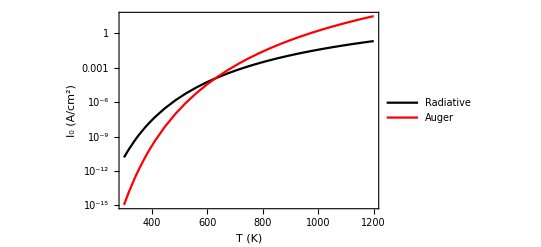

```mathematica
LogPlot[{10^-4 prefac  NemGuerra[0.726,T/300 Tcell,0,10^-5,0.005,3.5 10^4]/.constants,9 10^-28 nintrGaSb[T/300 Tcell]^3 echarge 10^-5/.constants},{T,300,1200},PerformanceGoal->"Speed",PlotRange->All,PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I_0 (A/cm^2)",""},{"T (K)","100 nm GaSb"}},PlotLegends->Placed[LineLegend[{"Radiative","Auger"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",5}],{0.75,0.36}]]
```

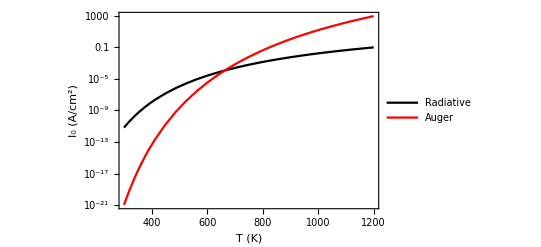

```mathematica
LogPlot[{10^-4 prefac NemGuerra[0.726,T/300 Tcell,0,10^-4,0.005,1.5 10^3]/.constants,10^-29 nintrSi[T/300 Tcell]^3 echarge 10^-3/.constants},{T,300,1200},PerformanceGoal->"Speed",PlotRange->All,PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I_0 (A/cm^2)",""},{"T (K)","Si"}},PlotLegends->Placed[LineLegend[{"Radiative","Auger"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",5}],{0.75,0.36}]]
```

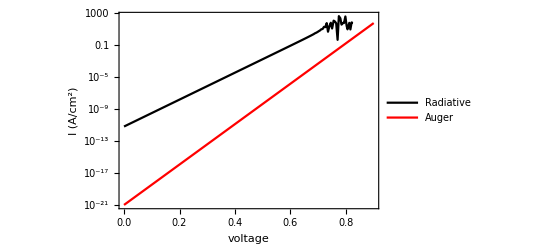

```mathematica
LogPlot[{10^-4 prefac NemGuerra[0.726,Tcell,voltage,10^-4,0.005,1.5 10^3]/.constants,10^-29 nintrSi[Tcell]^3 Exp[3 voltage/(2Tcell)]echarge 10^-3/.constants},{voltage,0,0.9},PerformanceGoal->"Speed",PlotRange->All,PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (A/cm^2)",""},{"voltage","Si"}},PlotLegends->Placed[LineLegend[{"Radiative","Auger"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",5}],{0.75,0.36}]]
```

```mathematica
(* absorption coefficient with a sqrt rise above the band edge *)
absCoeffUrbachSqrt[en_,Eg_,Eu_,rise_,absAboveBandgap_]:= HeavisideTheta[en-Eg]absAboveBandgap(1+rise Sqrt[en-Eg])+HeavisideTheta[Eg-en]absAboveBandgap Exp[(en-Eg)/Eu];
absorptivityUrbachSqrt[en_,Eg_,Eu_,rise_,absAboveBandgap_,thickness_]:= 1-Exp[-2absCoeffUrbachSqrt[en,Eg,Eu,rise,absAboveBandgap]thickness];
(* emitted/absorbed photon flux with Urbach tail and Bose Einstein distribution, neglecting angular dependence *)
NemUrbachSqrt[Eg_?NumericQ,T_?NumericQ,mu_?NumericQ,thickness_?NumericQ,Eu_?NumericQ,rise_?NumericQ,absAboveBandgap_?NumericQ]:=NIntegrate[absorptivityUrbachSqrt[en,Eg,Eu,rise,absAboveBandgap,thickness]/(Exp[(en-mu) / T]-1)en^2/.constants,{en,0,∞}];
currentTRDUrbachSqrtAuger[Eg_?NumericQ,Ttrd_?NumericQ,Tenv_?NumericQ,impactRate_?NumericQ,thickness_,Eu_?NumericQ,rise_?NumericQ,absAboveBandgap_?NumericQ,voltage_?NumericQ]:=10^-4 prefac/echarge NemUrbachSqrt[Eg,Ttrd,voltage,thickness,Eu,rise,absAboveBandgap]-10^-4(*to convert into cm^2*)prefac/echarge NemUrbachSqrt[Eg,Tenv,0,thickness,Eu,rise,absAboveBandgap]-(Exp[voltage/(2Ttrd)]-Exp[3 voltage/(2Ttrd)])impactRate thickness;
powerTRDAuger[Eg_,Ttrd_, Tenv_,impactRate_,thickness_,Eu_,rise_,absAboveBandgap_,voltage_]:= -currentTRDUrbachSqrtAuger[Eg,Ttrd,Tenv,impactRate,thickness,Eu,rise,absAboveBandgap,voltage]voltage echarge;
```

```mathematica
(* Germanium intrinsic carrier density *)
2 ((2 Pi Sqrt[me mh ] m0 echarge Tcell)/(2Pi hbar)^2)^(3/2)Exp[-Eg/(2Tcell)] 10^-6/.constants/.me->0.56/.mh->0.29/.Eg->0.66
(* In As intrinsic carrier density*)
2 ((2 Pi Sqrt[me mh ] m0 echarge Tcell)/(2Pi hbar)^2)^(3/2)Exp[-Eg/(2Tcell)] 10^-6/.constants/.me->0.023/.mh->0.41/.Eg->0.354
```

1.8355×10^13

8.0721×10^14

```mathematica
(* temperature dependence of intrinsic carrier concentration in InAs *)
nintrInAs[T_]:= 2 ((2 Pi Sqrt[me mh ] m0 echarge T)/(2Pi hbar)^2)^(3/2)Exp[-Eg/(2T)] 10^-6/.constants/.me->0.023/.mh->0.41/.Eg->0.354
nintrGaSb[T_]:= 2 ((2 Pi Sqrt[me mh ] m0 echarge T)/(2Pi hbar)^2)^(3/2)Exp[-Eg/(2T)] 10^-6/.constants/.me->0.041/.mh->0.4/.Eg->0.726
nintrSi[T_]:= 2 ((2 Pi Sqrt[me mh ] m0 echarge T)/(2Pi hbar)^2)^(3/2)Exp[-Eg/(2T)] 10^-6/.constants/.me->1.08/.mh->0.81/.Eg->1.12
```

```mathematica
nintrGaSb[4Tcell]
nintrSi[Tcell]
```

2.74955×10^17

8.88007×10^9

```mathematica
nintrInAs[ 2Tcell]
```

2.95077×10^16

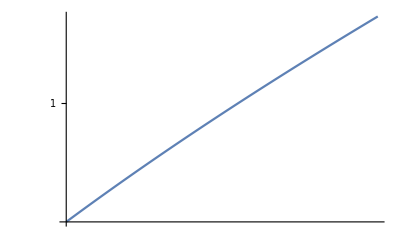

```mathematica
LogLogPlot[absGuerra[en,0.5,0.01,1],{en,1.2,1.8}]
```

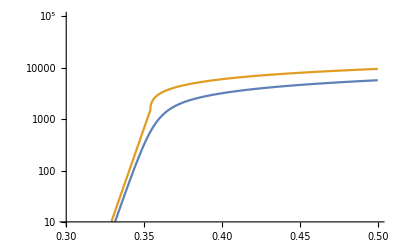

```mathematica
(* fitting to InAs absorption coefficient http://www.ioffe.ru/SVA/NSM/Semicond/InAs/optic.html*)
LogPlot[{absGuerra[en,0.354,0.005,1.5 10^4],absCoeffUrbachSqrt[en,0.354,0.005,14,1.5 10^3 thickness/.thickness->1(*cm*)]},{en,0.3,0.5},PlotRange->{10^1, 10^5}]
```

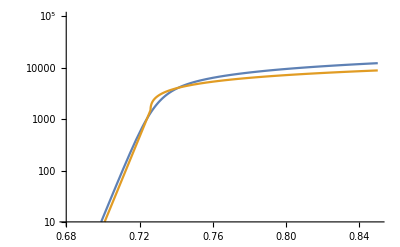

```mathematica
LogPlot[{absGuerra[en,0.726,0.005,3.5 10^4],absCoeffUrbachSqrt[en,0.726,0.005,14,1.5 10^3 thickness/.thickness->1(*cm*)]},{en,0.68,0.85},PlotRange->{10^1, 10^5}]
```

```mathematica
absorptivityGuerra[0.2,0.35,0.005,2.5 10^-4,10^-3]
```

General::munfl: Internal`AbsSquare[3.32244×10^-179-6.37832×10^-178 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1-ⅇ^(3.13329×10^-8 PolyLog[1/2,-9.35762×10^-14])

```mathematica
NemGuerra[0.35,Tcell/.constants,0,10^-3,0.005,2.5 10^-4]
currentTRDAugerGuerra[0.35,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,10^-3,0.005,2.5 10^4,0.02/1000]/.constants
```

3.87103×10^-16

1.2241×10^18

```mathematica
(* comparing the current calculated with the sqrt approximation to the absorptivity in the PolyLog approximation *)
Plot[{currentTRDUrbachSqrtAuger[0.35,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,10^-3,0.005,10,1.5 10^3,voltage/1000]/.constants,currentTRDAugerGuerra[0.35,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,10^-3,0.005,2.5 10^4,voltage/1000]/.constants},{voltage,-10 Tcell/.constants,0},PerformanceGoal->"Speed"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.347397}. NIntegrate obtained 0.000010981 and 3.2873×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.347397}. NIntegrate obtained 6.55257×10^-9 and 3.67049×10^-13 for the integral and error estimates.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.347397}. NIntegrate obtained 7.39637×10^-6 and 2.21382×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.347397}. NIntegrate obtained 6.55257×10^-9 and 3.67049×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.347397}. NIntegrate obtained 7.39637×10^-6 and 2.21382×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

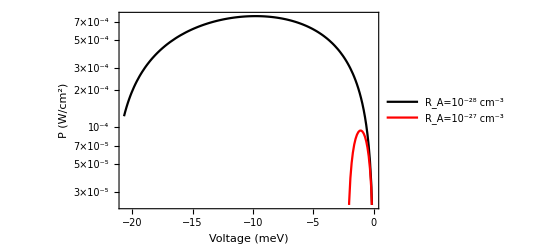

```mathematica
(* power generated by an ideal InAs device (no SRH) assuming different Auger rates, 10^-28 cm^-3 is the guess for p-type InAs in the Krier paper. n-type has much higher Auger rate and would therefore not be suitable *)
LogPlot[{powerTRDAuger[0.35,2Tcell/.constants,Tcell/.constants,10^-28(nintrInAs[2 Tcell])^3/.constants,10^-3,0.005,10,1.5 10^3,voltage/1000]/.constants,powerTRDAuger[0.35,2Tcell/.constants,Tcell/.constants,10^-27(nintrInAs[2 Tcell])^3/.constants,10^-3,0.005,10,1.5 10^3,voltage/1000]/.constants},{voltage,-800 Tcell/.constants,0},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/cm^2)",""},{"Voltage (meV)","10µm InAs, Td=600K, Tenv=300K"}},PerformanceGoal->"Speed",PlotLegends->{"R_A=10^-28 cm^-3","R_A=10^-27 cm^-3"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 5.70965×10^-6 and 3.57379×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 2.43386×10^-9 and 3.46192×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 2.28984×10^-6 and 1.55104×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

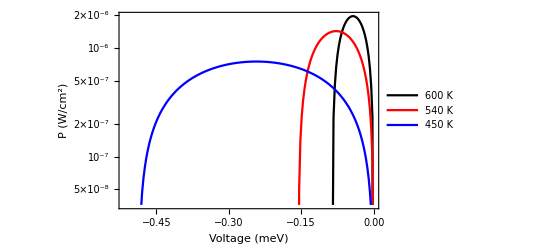

```mathematica
(* power generated by an ideal InAs device (no SRH) assuming different Auger rates, 10^-28 cm^-3 is the guess for p-type InAs in the Krier paper. n-type has much higher Auger rate and would therefore not be suitable *)
LogPlot[{powerTRDAuger[0.354,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,powerTRDAuger[0.354,1.8Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[1.8 Tcell])^3/.constants,10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,powerTRDAuger[0.354,1.5Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[1.5 Tcell])^3/.constants,10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants},{voltage,-20Tcell/.constants,0},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/cm^2)",""},{"Voltage (meV)","1 µm InAs, Td=600K, Tenv=300K"}},PerformanceGoal->"Speed",PlotLegends->{"600 K","540 K","450 K"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 3.59378×10^-6 and 2.03932×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 1.43856×10^-9 and 1.87727×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 5.75264×10^-6 and 3.60072×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

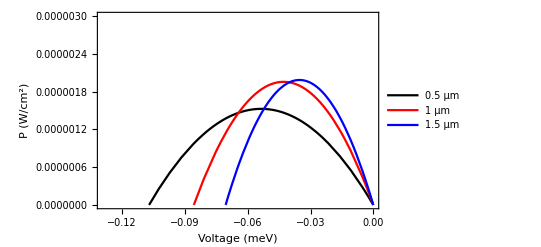

```mathematica
Plot[{powerTRDAuger[0.354,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,0.5 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,powerTRDAuger[0.354,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,1 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,powerTRDAuger[0.354,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,1.5 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants},{voltage,-5 Tcell/.constants,0},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/cm^2)",""},{"Voltage (meV)","intrinsic InAs, Td=600K, Tenv=300K"}},PlotRange->{0,0.000003},PerformanceGoal->"Speed",PlotLegends->{"0.5 μm","1 μm","1.5 μm"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 3.01711×10^-6 and 1.67962×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 1.19255×10^-9 and 1.52699×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 4.11473×10^-6 and 2.38085×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

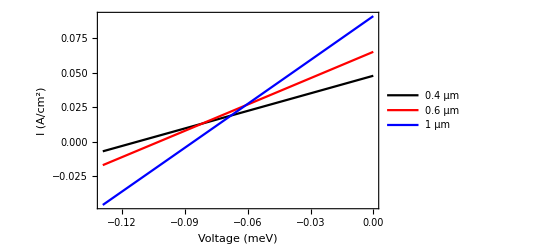

```mathematica
Plot[{echarge currentTRDUrbachSqrtAuger[0.354,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,0.4 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,echarge currentTRDUrbachSqrtAuger[0.354,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,0.6 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,echarge currentTRDUrbachSqrtAuger[0.354,2Tcell/.constants,Tcell/.constants,10^-26(nintrInAs[2 Tcell])^3/.constants,1 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants},{voltage,-5 Tcell/.constants,0},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (A/cm^2)",""},{"Voltage (meV)","intrinsic InAs, Td=600K, Tenv=300K"}},PerformanceGoal->"Speed",PlotLegends->{"0.4 μm","0.6 μm","1 μm"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 1.44434×10^-7 and 1.22327×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 2.43386×10^-9 and 3.46192×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {0.350952}. NIntegrate obtained 2.375×10^-7 and 1.23382×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

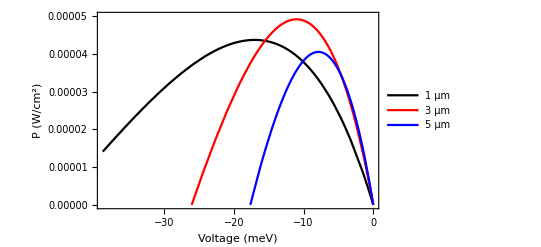

```mathematica
Plot[{powerTRDAuger[0.354,1.5Tcell/.constants,Tcell/.constants,10^-28(nintrInAs[1.5Tcell])^3/.constants,1 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,powerTRDAuger[0.354,1.5Tcell/.constants,Tcell/.constants,10^-28(nintrInAs[1.5 Tcell])^3/.constants,3 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants,powerTRDAuger[0.354,1.5Tcell/.constants,Tcell/.constants,10^-28(nintrInAs[1.5 Tcell])^3/.constants,5 10^-4,0.005,10,1.5 10^3,voltage/1000]/.constants},{voltage,-1500 Tcell/.constants,0},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (W/cm^2)",""},{"Voltage (meV)","p-type InAs, Td=450K, Tenv=300K"}},PlotRange->{0,0.00005},PerformanceGoal->"Speed",PlotLegends->{"1 μm","3 μm","5 μm"}]
```

### Boltzmann Distribution analytical

The goal here is find a way to analytically estimate the maximum power point in the presence of Auger recombination, so that it is possible to make a parameter study on the best combination of band gaps, temperatures and device thicknesses.

```mathematica
(* absorptivity for a diode with thickness d and a perfect mirror at the back and a perfect anti-reflection coating at the front *)
absorptivityEG[en_,Eg_,opticalThickness_]:= HeavisideTheta[en-Eg](1-Exp[-2 opticalThickness]);
```

```mathematica
(* energy flux in Boltzmann approximation *)
Integrate[(Exp[-en/T] en^2)en(* number of photons per energy x energy of each photon *),{en,Eg,∞},Assumptions->Eg>0&&T>0]
```

ⅇ^(-Eg/T) T (Eg^3+3 Eg^2 T+6 Eg T^2+6 T^3)

```mathematica
currentTRDAuger[Eg_,Ttrd_,Tenv_,thickness_,impactRate_,nintr300K_,absCoeff_,voltage_]:=(1-Exp[2 thickness absCoeff])(NemEGBoltzmann[Eg,Ttrd,voltage]-NemEGBoltzmann[Eg,Tenv,0])-(1-Exp[3voltage/(2Ttrd)])impactRate thickness (nintr300K Exp[Eg/Tcell] Exp[-Eg/Ttrd])^3;
powerTRDAuger[Eg_,Ttrd_,Tenv_,thickness_,impactRate_,nintr300K_,absCoeff_,voltage_]:= -voltage currentTRDAuger[Eg,Ttrd,Tenv,thickness,impactRate,nintr300K,absCoeff,voltage];
```

```mathematica
Solve[D[powerTRDAuger[Eg,Ttrd,Tenv,thickness,impactRate,nintr300K,absCoeff,voltage],voltage]==0,voltage]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^((3 Eg)/Tcell-(3 Eg)/Ttrd) (1-ⅇ^(3 voltage/2)) impactRate nintr300K^3 thickness-(1-ⅇ^(2 absCoeff thickness)) (-ⅇ^(-Eg/Tenv) Tenv (Eg^2+2 Eg Tenv+2 Tenv^2)+ⅇ^(-(Eg-voltage)/Ttrd) Ttrd (Eg^2+2 Eg Ttrd+2 Ttrd^2))-(3/2 ⅇ^((3 Eg)/Tcell-(3 Eg)/Ttrd+(3 voltage)/2) impactRate nintr300K^3 thickness+ⅇ^(-(Eg-voltage)/Ttrd) (1-ⅇ^(2 absCoeff thickness)) (Eg^2+2 Eg Ttrd+2 Ttrd^2)) voltage==0,voltage]

```mathematica
Solve[currentTRDAuger[Eg,Ttrd,Tenv,thickness,impactRate,nintr300K,absCoeff,voltage]==0,voltage]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-ⅇ^((3 Eg)/Tcell-(3 Eg)/Ttrd) (1-ⅇ^(3 voltage/2)) impactRate nintr300K^3 thickness+(1-ⅇ^(2 absCoeff thickness)) (-ⅇ^(-Eg/Tenv) Tenv (Eg^2+2 Eg Tenv+2 Tenv^2)+ⅇ^(-(Eg-voltage)/Ttrd) Ttrd (Eg^2+2 Eg Ttrd+2 Ttrd^2))==0,voltage]

auger Exp[3Eg/Ttrd](1-Exp[3V/(2Ttrd)]) + absorptivity ((Exp[-Eg/Ttrd] Exp[-V/Ttrd] Ttrd Eg^2-Exp[-Eg/Tenv]Tenv Eg^2))==0

```mathematica
xsol=Solve[a(1-x^(3/2))+b x - c==0,x];
```

```mathematica
D[(a(1-Exp[3x/2])+b Exp[x]-c)x,x]
```

-c+b ⅇ^x+a (1-ⅇ^(3 x/2))+(b ⅇ^x-3/2 a ⅇ^(3 x/2)) x

```mathematica
Solve[-c+b ⅇ^x+a (1-ⅇ^(3 x/2))+(b ⅇ^x-3/2 a ⅇ^(3 x/2)) x==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
Solve[-c+b ⅇ^x+a (1-ⅇ^x)+(b ⅇ^x-3/2 a ⅇ^x) x==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-2 a+2 b+3 a ProductLog[(2 (a-c) ⅇ^((2 a)/(3 a-2 b)-(2 b)/(3 a-2 b)))/(3 a-2 b)]-2 b ProductLog[(2 (a-c) ⅇ^((2 a)/(3 a-2 b)-(2 b)/(3 a-2 b)))/(3 a-2 b)])/(3 a-2 b)}}

```mathematica
Solve[-c+b x+a (1-x)+(b x- a x) Log[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(a-c)/((a-b) ProductLog[((a-c) (ⅇ^(-1+b/a))^(-a/(a-b)))/(a-b)])}}

## Checking Myles' paper

```mathematica
ITRtoPV[VTR_,VPV_,Ta_] := prefac(NemEGPrecise[0.5,Ta,VTR]-NemEGPrecise[0.5,Tcell,VPV])/.constants;
energyBalance[VTR_,VPV_,f_,Ta_]:=f  emissionEnergyEGBoltzmann[0.9,20 Tcell,0]- emissionEnergyEGBoltzmann[0.9,Ta,0]- EnemEGPrecise[0.5,Ta, VTR]+ EnemEGPrecise[0.5,Tcell,VPV]/.constants;
Tafun[VTR_,VPV_,f_]:= Ta /. FindRoot[energyBalance[VTR,VPV,f,Ta]==0,{Ta,1000}]
powerOut[VTR_,VPV_,Ta_]:=- ITRtoPV[VTR,VPV,Ta] (VTR-VPV); 
powerOutNR[VTR_,VPV_,Ta_,etaExt_]:= ITRtoPV[VTR,VPV,Ta]VPV-VTR (ITRtoPV[VTR,VPV,Ta]-prefac NemEGPrecise[0.3,Ta,VTR]/etaExt(1-Exp[VTR/Ta]))/.constants;
```

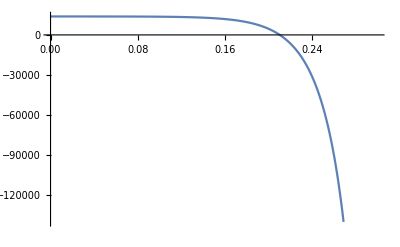

```mathematica
Plot[ITRtoPV[-0.025,VPV,800/300 Tcell],{VPV,0,0.3}]
```

```mathematica
Tafun[-0.025,0.22,1/46620]300 /Tcell/.constants
ITRtoPV[-0.025,0.22,847.286/300 Tcell]
powerOut[-0.025,0.22,Tafun[-0.025,0.22,1/46620]]/( sigma (20 Tcell)^4/46620)/.constants
```

847.286

-663.235

-0.103089

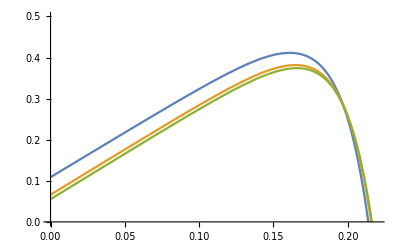

```mathematica
Plot[{powerOut[-0.05,VPV,Tafun[-0.05,VPV,1/46620]]/( sigma (20 Tcell)^4/46620)/.constants,
powerOut[-0.03,VPV,Tafun[-0.03,VPV,1/46620]]/( sigma (20 Tcell)^4/46620)/.constants,powerOut[-0.025,VPV,Tafun[-0.025,VPV,1/46620]]/( sigma (20 Tcell)^4/46620)/.constants},{VPV,0,0.22},PerformanceGoal->"Speed",PlotRange->{0,0.5}]
```

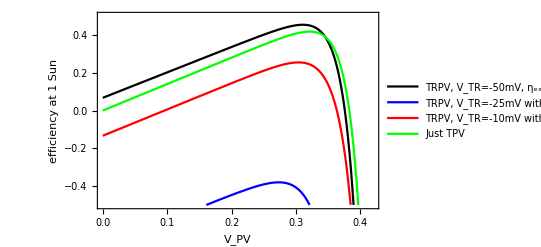

```mathematica
Plot[{powerOut[-0.05,VPV,Tafun[-0.05,VPV,1/46620]]/( sigma (20 Tcell)^4/46620)/.constants,
powerOutNR[-0.025,VPV,Tafun[-0.025,VPV,1/46620],0.1]/( sigma (20 Tcell)^4/46620)/.constants,
powerOutNR[-0.01,VPV,Tafun[-0.01,VPV,1/46620],0.1]/( sigma (20 Tcell)^4/46620)/.constants,powerOutNR[0,VPV,Tafun[0,VPV,1/46620],0.01]/( sigma (20 Tcell)^4/46620)/.constants},{VPV,0,0.42},PlotStyle->{Black,Blue,Red,Green},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"efficiency at 1 Sun",""},{"V_PV","E_g=0.5eV"}},PerformanceGoal->"Speed",PlotRange->{-0.5,0.5},PlotLegends->Placed[LineLegend[{"TRPV, V_TR=-50mV, η_ext=1","TRPV, V_TR=-25mV with η_ext=0.1","TRPV, V_TR=-10mV with η_ext=0.1","Just TPV"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.5,0.25}]]
```

## Checking HgCdTe paper

```mathematica
Solve[n (n-nD)==ni Exp[V/T],n]
```

{{n→1/2 (nD-√(nD^2+4 ⅇ^(V/T) ni))},{n→1/2 (nD+√(nD^2+4 ⅇ^(V/T) ni))}}

```mathematica
Egfun[x_,T_]:= -0.302 + 1.93 x -0.81 x^2+0.832 x^3+5.35 10^-4(1-2 x) T 300/Tcell ;(*Hansen et al. "Energy gap versus alloy composition and temperature in Hg1−xCdxTe", Journal of Applied Physics 53,7099 (1982)*)
Egfun[0.126,Tcell]/.constants
tAuger[Eg_,T_] := 8.3 10^-13 Eg^(1/2)T^(-3/2)Exp[Eg/T];(*Equation (8) of Zheng2020, also in Wikipedia and equation 18 in Rogalski review*)
tAug=tAuger[0.05,Tcell/.constants]
ni[T_,x_,Eg_]:=10^6(* convert to m^-3*)(5.585-3.82 x +0.001753 T 300/Tcell-0.001364 x T 300/Tcell)10^14 Eg^(3/4)(T 300/Tcell)^(3/2)Exp[-Eg/(2T)]; (* equation (7) of Zhang2020*)
ni[Tcell,0.126,Egfun[0.126,Tcell]]/.constants
nReal[nD_,T_,x_,Eg_,V_] := 1/2(nD+Sqrt[nD^2+4 Exp[V/T] ni[T,x,Eg]^2]);
pReal[nD_,T_,x_,Eg_,V_] := nReal[nD,T,x,Eg,V]-nD;
jAugOld[T_,tAuge_,thickness_,nintrinsic_,voltage_]:= echarge thickness ((Exp[voltage/T]-1)/2) (nintrinsic Exp[voltage/(2T)])/((1+ 5.26 10^-24 nintrinsic  Exp[voltage/(2T)])tAuge) ;
jAugZheng[T_,tAuge_,thickness_,nintrinsic_,voltage_]:= echarge thickness (1/(2 nintrinsic^2)(nReal[10^21,T,0.126,Egfun[0.126,T],voltage] pReal[10^21,T,0.126,Egfun[0.126,T],voltage]-nintrinsic^2)) nReal[10^21,T,0.126,Egfun[0.126,T],voltage]/((1+nReal[10^21,T,0.126,Egfun[0.126,T],voltage]5.26 10^-24)tAuge) ;(*first part of equation (6) of Zhang2020*)
jSRHZheng[T_,tauSRH_,thickness_,nintrinsic_,voltage_]:=echarge (thickness/tauSRH)((nReal[10^21,T,0.126,Egfun[0.126,T],voltage]pReal[10^21,T,0.126,Egfun[0.126,T],voltage]-nintrinsic^2)/(nReal[10^21,T,0.126,Egfun[0.126,T],voltage]+pReal[10^21,T,0.126,Egfun[0.126,T],voltage] +2nintrinsic));(* second part of equation (6) of Zhang2020*)
jSRHZheng[Tcell,10^-6,10^-7,10^23,- Tcell]/.constants
jAugZheng[Tcell,tAug,10^-7,10^23,- Tcell]/.constants

currentZhang= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","ZhangIV.csv"}]];
ivZhang = Delete[currentZhang,{1}];
interZhang = Interpolation[ivZhang];
```

0.0500388

3.08877×10^-10

1.16502×10^23

-235.019

-672405.

```mathematica
(* attempt to replicate Zhang's curve by inserting the wrong units. This was suggested by reviewer 2 *)
jAugWrongUnits[T_,tAuge_,thickness_,nintrinsic_,voltage_]:= echarge thickness (1/(2 nintrinsic^2)(nReal[10^21,T,0.126,Egfun[0.126,T],voltage] pReal[10^21,T,0.126,Egfun[0.126,T],voltage]-nintrinsic^2)) (nReal[10^21,T,0.126,Egfun[0.126,T],voltage] 10^-6)/((1+nReal[10^21,T,0.126,Egfun[0.126,T],voltage]5.26 10^-24)tAuge) ;
jSRHWrongUnits[T_,tauSRH_,thickness_,nintrinsic_,voltage_]:=echarge (thickness/tauSRH)10^-6((nReal[10^21,T,0.126,Egfun[0.126,T],voltage]pReal[10^21,T,0.126,Egfun[0.126,T],voltage]-nintrinsic^2)/(nReal[10^21,T,0.126,Egfun[0.126,T],voltage]+pReal[10^21,T,0.126,Egfun[0.126,T],voltage] +2nintrinsic));
emissionZheng[voltage_]:= prefac currentTRD[2 Pi hbar clight /echarge 10^6/13,Tcell/.constants,3 Tcell/300/.constants,voltage]-prefac currentTRD[2 Pi hbar clight /echarge 10^6/8,Tcell/.constants,3 Tcell/300/.constants,voltage]
currentZheng[voltage_]:= 132.6+ jAugWrongUnits[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]+jSRHWrongUnits[Tcell,10^-6,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage];
powerZheng[voltage_]:=voltage (emissionZheng[voltage] + jAugWrongUnits[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]+jSRHWrongUnits[Tcell,10^-6,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]);
```

```mathematica
FindRoot[currentZheng[voltage]==0/.constants,{voltage,-0.150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{voltage→-0.0349025}

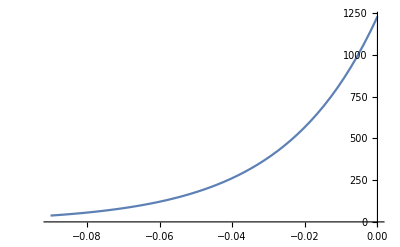

```mathematica
Plot[{emissionZheng[voltage]/.constants},{voltage,-0.09,0}]
```

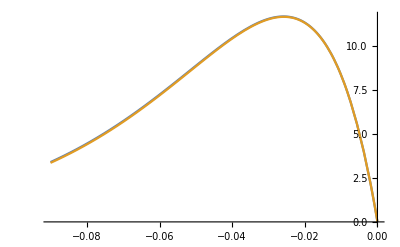

```mathematica
Plot[{-voltage emissionZheng[voltage]/.constants,-powerZheng[voltage]/.constants},{voltage,-0.09,0}]
```

```mathematica
2 Pi hbar clight /echarge 10^6/13 /.constants
```

0.0953725

```mathematica
2.12 10^-14/0.221^2 (* Prefactor of the undoped Auger lifetime according to Kinch2005 *)
(2  2.12 10^-14/0.221^2)/(1+(ni[Tcell,0.126,Egfun[0.126,Tcell]]/nReal[10^21,Tcell,0.126,Egfun[0.126,Tcell],0])^2)/.constants(* prefactor of Auger lifetime for doped material according to Wikipedia, supposedly from Redfern2001 but that has a slightly different functional form *)
```

4.34062×10^-13

4.35924×10^-13

```mathematica
(jAug[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],-2Tcell]/jAugOld[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],-2Tcell])/.constants
```

2.06455

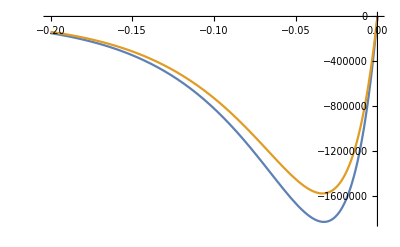

```mathematica
(*T_,x_,thickness_,doping_,voltage*)
Plot[{jAugRogalski[Tcell,0.126,1.8 10^-7,10^21,voltage]/.constants,jAugZheng[Tcell,tAug,1.8 10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]/.constants},{voltage,-0.2,0}]
```

```mathematica
jAugZheng[Tcell,tAug,1.8 10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],-0.150 ]/.constants
jAugOld[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],-Tcell]/.constants
jSRH[Tcell, 10^-6,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],-Tcell]/jSRHZheng[Tcell, 10^-6,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],-Tcell]/.constants
```

-310878.

-844557.

-0.00272319 jSRH[0.025852,1/1000000,1/10000000,1.16502×10^23,-0.025852]

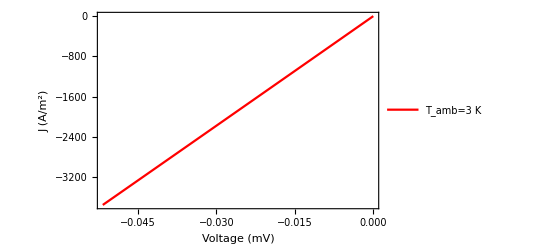

```mathematica
Plot[{currentTRD[0.05,Tcell/.constants,3 Tcell/300/.constants,voltage/1000]+jAugZheng[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage/1000]/.constants},{voltage,-2 Tcell/.constants,0},PlotStyle->{Black,Blue,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"J (A/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotRange->All,PlotLegends->Placed[LineLegend[{"T_amb=3 K","T_amb=200 K","T_amb=280 K"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.2,0.75}]]
```

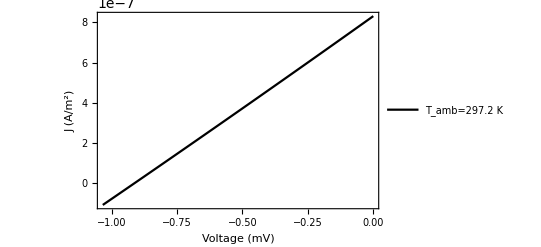

```mathematica
Plot[{currentTRD[0.05,Tcell/.constants,297.2 Tcell/300/.constants,voltage/1000]/.constants},{voltage,-40 Tcell/.constants,0},PlotStyle->{Black},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"J (A/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotRange->All,PlotLegends->Placed[LineLegend[{"T_amb=297.2 K","T_amb=200 K","T_amb=280 K"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.2,0.75}]]
```

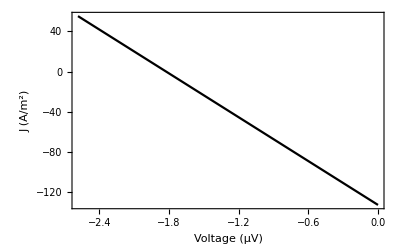

```mathematica
(* Calculating the I-V curve using only the nonradiative part of the exchange plus the short circuit current quoted in Figure 3b of Zhang2020 *)
Plot[{-132.6(Exp[voltage/(1000000 Tcell)])-jSRHZheng[Tcell,10^-6,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage/1000000]-jAugZheng[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage/1000000]/.constants},{voltage,-100Tcell/.constants,0},PlotStyle->{Black},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"J (A/m^2)",""},{"Voltage (μV)",""}},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
FindRoot[(-132.6(Exp[voltage/( Tcell)])-jSRHZheng[Tcell,10^-6,1.8 10^-6,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]-jAugZheng[Tcell,tAug,1.8 10^-6,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage])/.constants,{voltage,10^-6}]
FindRoot[(-132.6(Exp[voltage/( Tcell)])-10^-4 jSRHZheng[Tcell,10^-6,1.8 10^-6,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]-10^-6 jAugZheng[Tcell,tAug,1.8 10^-6,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage])/.constants,{voltage,10^-1}]
```

{voltage→-1.01357×10^-7}

{voltage→-0.0570079}

```mathematica
10^6 voltage(-132.6(Exp[voltage/( Tcell)])-jSRHZheng[Tcell,10^-6,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]-jAugZheng[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage])/.voltage->-1.8244 10^-6/2/.constants
```

60.4772

InterpolatingFunction::dmval: Input value {-0.0899963} lies outside the range of data in the interpolating function. Extrapolation will be used.

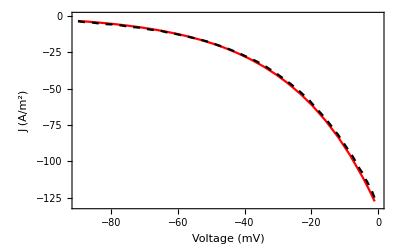

```mathematica
(* Using the incorrect formalism in the paper for the radiative part and the correct formalism with unit conversion errors for the nonradiative part *)
Plot[{-132.6(Exp[voltage/(1000 Tcell)])-10^-3 jSRHZheng[Tcell,10^-6,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage/1000]-10^-8 jAugZheng[Tcell,tAug,10^-7,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage/1000]/.constants,100 interZhang[voltage/1000]},{voltage,-90/.constants,-1},PlotStyle->{Red,{Black,Dashed}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"J (A/m^2)",""},{"Voltage (mV)",""}},PerformanceGoal->"Speed",PlotRange->{-130,0}]
```

```mathematica
vZhang[[2]]
```

-0.0890389

```mathematica
FindRoot[(-132.6(Exp[voltage/(Tcell)])-10^-4 jSRHZheng[Tcell,10^-6,1.8 10^-6,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage])-10^-6 jAugZheng[Tcell,tAug,1.8 10^-6,ni[Tcell,0.126,Egfun[0.126,Tcell]],voltage]/.constants,{voltage,-10^-2}]
```

{voltage→-0.0570079}

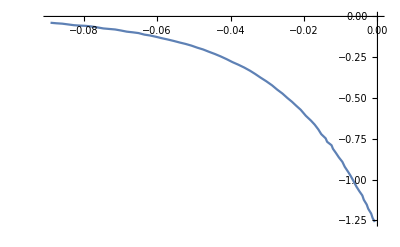

InterpolatingFunction::dmval: Input value {-0.0899982} lies outside the range of data in the interpolating function. Extrapolation will be used.

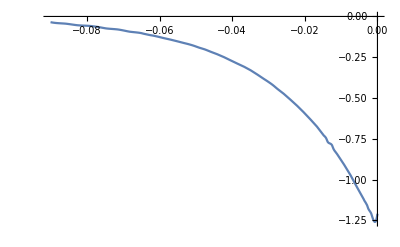

```mathematica
iZhang = Transpose[currentZhang][[2]];
vZhang = Transpose[currentZhang][[1]];
ListPlot[currentZhang,Joined->True]
ivZhang = Delete[currentZhang,{1}];
interZhang = Interpolation[ivZhang];
Plot[interZhang[x],{x,-0.09,0}]
```

## Calculating I - V curves for the 6 micron HgCdTe diode

TODO estimate series resistance from total EL curves provided by Michael

## Fresnel equations and their consequences

```mathematica
reflSpol[thetain_,n1_,n2_]:= Abs[(n1 Cos[thetain]-n2 Sqrt[1-n1^2 Sin[thetain]^2/n2^2])/(n1 Cos[thetain]+n2 Sqrt[1-n1^2 Sin[thetain]^2/n2^2])]^2;
reflPpol[thetain_,n1_,n2_]:= Abs[(n1  Sqrt[1-n1^2 Sin[thetain]^2/n2^2]-n2 Cos[thetain])/(n1 Sqrt[1-n1^2 Sin[thetain]^2/n2^2]+n2 Cos[thetain])]^2;
```

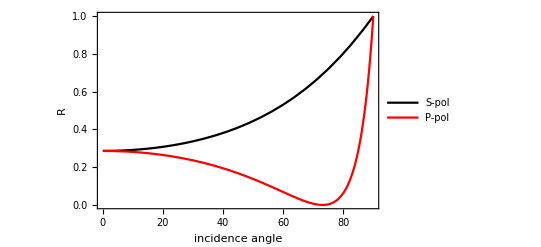

```mathematica
Plot[{reflSpol[theta Pi/180,1,nLens],reflPpol[theta Pi/180,1,nLens]},{theta,0,90},PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"R",""},{"incidence angle","Fresnel equations for n=3.3"}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"S-pol","P-pol"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.5,0.75}]]
```

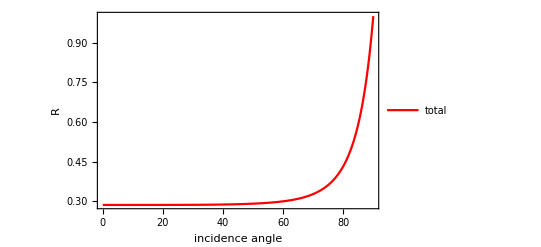

```mathematica
Plot[{(reflSpol[theta Pi/180,1,nLens]+reflPpol[theta Pi/180,1,nLens])/2},{theta,0,90},PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"R",""},{"incidence angle","Fresnel equations for n=3.3"}},PerformanceGoal->"Speed",PlotRange->All,PlotLegends->Placed[LineLegend[{"total","P-pol"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.5,0.75}]]
```

```mathematica
NIntegrate[reflSpol[theta,nLens,1] Sin[theta]Cos[theta] ,{theta,0,ArcSin[1/nLens]}]/Integrate[Sin[theta]Cos[theta],{theta,0,ArcSin[1/nLens]}]
NIntegrate[reflPpol[theta,nLens,1] Sin[theta]Cos[theta] ,{theta,0,ArcSin[1/nLens]}]/Integrate[Sin[theta]Cos[theta],{theta,0,ArcSin[1/nLens]}]
```

0.451956

0.159479

## EL spectra of our Diodes

First step : get the EQE curve of the diode

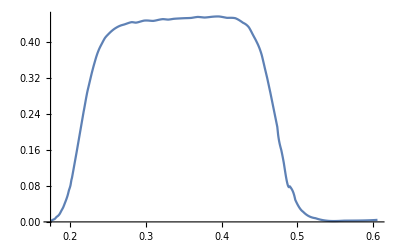

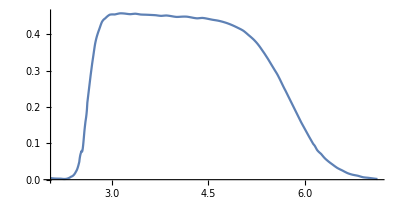

```mathematica
eqe6micronData= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","corrected_EQE_6um_diode.csv"}]];
eqe6wl = Transpose[eqe6micronData][[3]];
wl6 = Transpose[eqe6micronData][[1]];
energy6 = 2 Pi hbar clight 10^6/echarge/wl6/.constants;
energy6 =Delete[energy6,{1}];
energy6 = Delete[energy6,{1}];
(* export data of EL plot *)
wl6= Delete[wl6,{1}];
wl6 = Delete[wl6,{1}];
eqe6 = Delete[eqe6wl,{1}];
eqe6 = Delete[eqe6,{1}]/100;
eqeFun = Interpolation[Transpose[{energy6,eqe6}]];
Plot[eqeFun[x],{x,Min[energy6],Max[energy6]}]
ParametricPlot[{2 Pi hbar clight 10^6/echarge/x/.constants,eqeFun[x]},{x,Min[energy6],Max[energy6]},AspectRatio->1/2]
```

```mathematica
integratedEL= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","integratedELsignal.csv"}]];
integratedEL6muVoltage = Transpose[integratedEL][[1]];
integratedEL6muSignal = Transpose[integratedEL][[2]];
el6V = Delete[Delete[Delete[integratedEL6muVoltage,{1}],{1}],{1}];
el6S = Delete[Delete[Delete[integratedEL6muSignal,{1}],{1}],{1}];
```

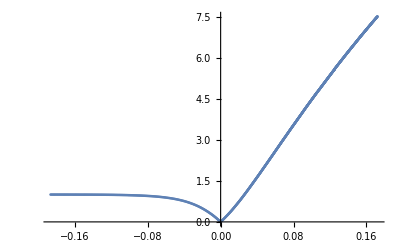

```mathematica
ListPlot[Transpose[{el6V,el6S}]]
```

Expected emission spectrum

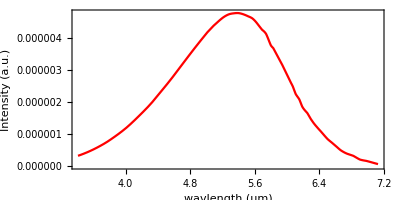

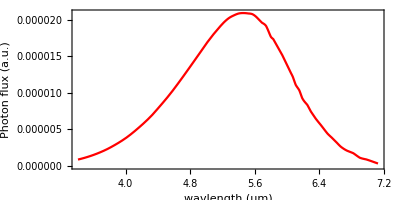

```mathematica
ParametricPlot[{2 Pi hbar clight 10^6/echarge/energy/.constants,eqeFun[energy] 2 Pi hbar clight /echarge/energy^-5 prefac/(Exp[(energy)/(293 Tcell/300)]-1)/.constants},{energy,Min[energy6],0.6 Max[energy6]},AspectRatio->1/2,PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Intensity (a.u.)",""},{"wavlength (μm)","EL spectrum of diode from EQE"}}]
ParametricPlot[{2 Pi hbar clight 10^6/echarge/energy/.constants,eqeFun[energy]2 Pi hbar clight /echarge/energy^-4 prefac/(Exp[(energy)/(293 Tcell/300)]-1)/.constants},{energy,Min[energy6],0.6 Max[energy6]},AspectRatio->1/2,PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Photon flux (a.u.)",""},{"wavlength (μm)","EL spectrum of diode from EQE"}}]
```

```mathematica
EL6 = eqeFun[2 Pi hbar clight 10^6/echarge/wl6/.constants] wl6^-4 prefac/(Exp[(2 Pi hbar clight 10^6/echarge/wl6)/(293 Tcell/300)]-1)/.constants;
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EL6micron.csv"}],{EL6,wl6}]
```

C:\Users\z3524693\Dropbox\Thermoradiative diode\Calculations\EL6micron.csv

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EL6micronAngularIntegral.csv"}],{EL6precise,wl6}]
```

C:\Users\z3524693\Dropbox\Thermoradiative diode\Calculations\EL6micronAngularIntegral.csv

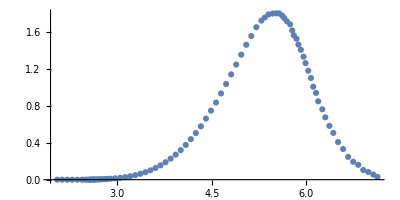

```mathematica
ListPlot[Transpose[{wl6,EL6precise}],AspectRatio->1/2]
```

```mathematica
eqe4
```

{(Using 2.1A/W at 4um from data sheet)/100,0.00494091,0.00413099,0.00783272,0.0186467,0.040596,0.0690212,0.097437,0.126931,0.161574,0.200275,0.234358,0.26503,0.295682,0.327405,0.360335,0.389848,0.415474,0.44212,0.466569,0.487419,0.50359,0.52479,0.528108,0.530992,0.532862,0.544506,0.542936,0.54948,0.536867,0.542894,0.541424,0.539071,0.54616,0.542609,0.543281,0.543646,0.543135,0.541204,0.542994,0.539148,0.541753,0.542932,0.540834,0.537974,0.535704,0.536634,0.535204,0.533287,0.533703,0.527039,0.529009,0.524003,0.518602,0.51938,0.515808,0.511109,0.503895,0.501966,0.498911,0.493148,0.487715,0.477855,0.471928,0.461976,0.447298,0.43396,0.415803,0.398455,0.3812,0.365194,0.348377,0.331167,0.316325,0.299469,0.284107,0.271287,0.259088,0.244519,0.228973,0.215674,0.196232,0.1861,0.17594,0.162995,0.148876,0.134783,0.120546,0.105449,0.0912235,0.0765433,0.0630976,0.0491461,0.03783,0.0283731,0.0205483,0.0148771,0.010786,0.00542201,0.00215662,0.00218421,0.00221142,0.00294999,0.00438536,0.00474813,0.00545283}

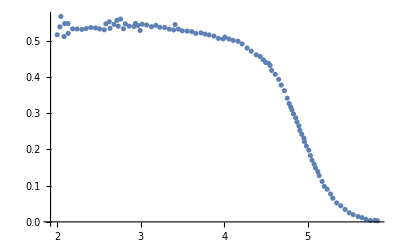

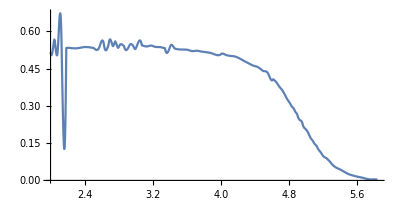

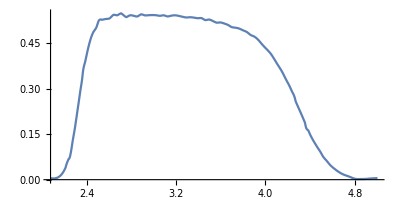

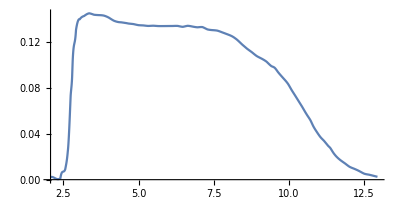

```mathematica
eqe5micronData= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EQE_5um_diode.csv"}]];
eqe5wl = Transpose[eqe5micronData][[4]];
wl5 = Transpose[eqe5micronData][[1]];
(* export data of EL plot *)
wl5= Delete[wl5,{1}];
wl5 = Delete[wl5,{1}];
wl5 = Delete[wl5,{1}];
energy5 = 2 Pi hbar clight 10^6/echarge/wl5/.constants;
eqe5 = Delete[eqe5wl,{1}];
eqe5 = Delete[eqe5,{1}];
eqe5 = Delete[eqe5,{1}]/100;
eqeFun5= Interpolation[Transpose[{energy5,eqe5}]];
ListPlot[Transpose[{wl5,eqe5}]]
ParametricPlot[{2 Pi hbar clight 10^6/echarge/x/.constants,eqeFun5[x]},{x,Min[energy5],Max[energy5]},AspectRatio->1/2,PlotRange->All]
eqe4micronData= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EQE_4um_diode.csv"}]];
eqe4wl = Transpose[eqe4micronData][[4]];
wl4 = Transpose[eqe4micronData][[1]];
(* export data of EL plot *)
wl4= Delete[wl4,{1}];
wl4 = Delete[wl4,{1}];
wl4 = Delete[wl4,{1}];
energy4 = 2 Pi hbar clight 10^6/echarge/wl4/.constants;
eqe4 = Delete[eqe4wl,{1}];
eqe4 = Delete[eqe4,{1}];
eqe4 = Delete[eqe4,{1}]/100;
eqeFun4 = Interpolation[Transpose[{energy4,eqe4}]];
ParametricPlot[{2 Pi hbar clight 10^6/echarge/x/.constants,eqeFun4[x]},{x,Min[energy4],Max[energy4]},AspectRatio->1/2]
eqe10micronData= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EQE_10-6um_diode.csv"}]];
eqe10wl = Transpose[eqe10micronData][[3]];
wl10 = Transpose[eqe10micronData][[1]];
(* export data of EL plot *)
wl10= Delete[wl10,{1}];
wl10 = Delete[wl10,{1}];
energy10 = 2 Pi hbar clight 10^6/echarge/wl10/.constants;
eqe10 = Delete[eqe10wl,{1}];
eqe10 = Delete[eqe10,{1}]/100;
eqeFun10 = Interpolation[Transpose[{energy10,eqe10}]];
ParametricPlot[{2 Pi hbar clight 10^6/echarge/x/.constants,eqeFun10[x]},{x,Min[energy10],Max[energy10]},AspectRatio->1/2]
```

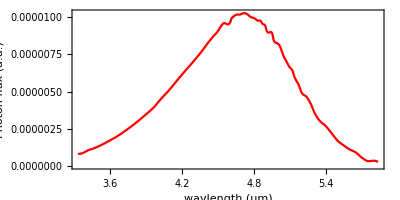

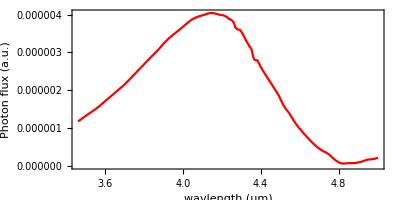

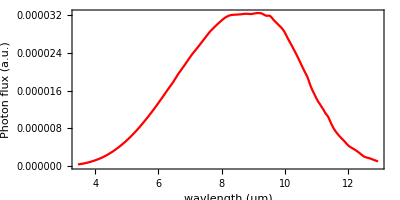

```mathematica
ParametricPlot[{2 Pi hbar clight 10^6/echarge/energy/.constants,eqeFun5[energy]2 Pi hbar clight /echarge/energy^-4 prefac/(Exp[(energy)/(293 Tcell/300)]-1)/.constants},{energy,Min[energy5],0.6 Max[energy5]},AspectRatio->1/2,PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Photon flux (a.u.)",""},{"wavlength (μm)","EL 5 μm diode from EQE"}}]
ParametricPlot[{2 Pi hbar clight 10^6/echarge/energy/.constants,eqeFun4[energy]2 Pi hbar clight /echarge/energy^-4 prefac/(Exp[(energy)/(293 Tcell/300)]-1)/.constants},{energy,Min[energy4],0.6 Max[energy4]},AspectRatio->1/2,PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Photon flux (a.u.)",""},{"wavlength (μm)","EL 4 μm diode from EQE"}}]
ParametricPlot[{2 Pi hbar clight 10^6/echarge/energy/.constants,eqeFun10[energy]2 Pi hbar clight /echarge/energy^-4 prefac/(Exp[(energy)/(293 Tcell/300)]-1)/.constants},{energy,Min[energy10],0.6 Max[energy10]},AspectRatio->1/2,PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Photon flux (a.u.)",""},{"wavlength (μm)","EL 10 μm diode from EQE"}}]
```

```mathematica
EL5 = eqeFun5[2 Pi hbar clight 10^6/echarge/wl5/.constants] wl5^-4 prefac/(Exp[(2 Pi hbar clight 10^6/echarge/wl5)/(293 Tcell/300)]-1)/.constants;
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EL5micron.csv"}],{EL5,wl5}]
EL4 = eqeFun4[2 Pi hbar clight 10^6/echarge/wl4/.constants] wl4^-4 prefac/(Exp[(2 Pi hbar clight 10^6/echarge/wl4)/(293 Tcell/300)]-1)/.constants;
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EL4micron.csv"}],{EL4,wl4}]
EL10 = eqeFun10[2 Pi hbar clight 10^6/echarge/wl10/.constants] wl10^-4 prefac/(Exp[(2 Pi hbar clight 10^6/echarge/wl10)/(293 Tcell/300)]-1)/.constants;
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","EL10micron.csv"}],{EL10,wl10}]
```

/Users/andreaspusch/Dropbox/Thermoradiative diode/Calculations/EL5micron.csv

/Users/andreaspusch/Dropbox/Thermoradiative diode/Calculations/EL4micron.csv

/Users/andreaspusch/Dropbox/Thermoradiative diode/Calculations/EL10micron.csv

## Calculating emission from the Lens

```mathematica
(* calculating intercept between emitted ray and circle *)
emittedRayX[z_] := Tan[beta] (z+r/n) + d;
circleX[z_]:= Sqrt[r^2-z^2]  ;
zsol = Solve[{emittedRayX[z]==circleX[z]},z][[2]]
```

{z→(-2 d Tan[beta]-(2 r Tan[beta]^2)/n+√(-4 d^2+4 r^2-(8 d r Tan[beta])/n+4 r^2 Tan[beta]^2-(4 r^2 Tan[beta]^2)/n^2))/(2 (1+Tan[beta]^2))}

```mathematica
vector1 = {x1,y1};
vector2 = {x2,y2};
vector1.vector2
```

x1 x2+y1 y2

```mathematica
Animate[radius=0.8;
nLens = 3.3;
(*beta1 = Pi/10;*) (* angular position where ray hits the surface of the lens *)
(*xE =0.1;*) (* x position of ray leaving the device *)
yD = -radius/nLens;(* y position of the device *)
zint = z/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE;
xint = emittedRayX[z]/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE;
line1 = {xint-xE,zint-yD};
line2 = {xint,zint};
If[(Pi/2-beta1>=ArcTan[yD/xE]&&xE<0)(*||(xE>0)*),alpha =ArcCos[( line1.line2)/Sqrt[line1.line1  line2.line2]],alpha =-ArcCos[( line1[[1]]line2[[1]]+line1[[2]]line2[[2]])/Sqrt[(line1[[1]]^2+line1[[2]]^2)(line2[[1]]^2+line2[[2]]^2)]]];
alphaOut = HeavisideTheta[1-Abs[nLens Sin[alpha]]]ArcSin[nLens Sin[alpha]]+HeavisideTheta[Abs[nLens Sin[alpha]]-1](-Pi);
alphaOut 180/Pi;
alpha 180/Pi;
ceta =HeavisideTheta[zint]ArcTan[xint/zint]+HeavisideTheta[-zint](Pi+ArcTan[xint/zint]);
outAngle = alphaOut+ceta ;
outAngle 180/Pi;
ceta 180/Pi;
Graphics[{Black,Circle[{0,0},radius,{-ArcSin[1/nLens],Pi+ArcSin[1/nLens]}],Opacity[0.2],Rectangle[{-0.5,-0.5},{0.5,yD }],Opacity[1],Line[{{xE,yD},{xE+2  Sin[beta1] radius,yD +2 Cos[beta1] radius}}],Circle[{xint,zint},0.3,{ArcTan[zint/xint],ArcTan[zint/xint]-alpha}],Red,Circle[{0,0},-yD/1.5,{Pi/2-ceta,Pi/2}],Circle[{xE,yD},0.5,{0,Pi/2-beta1}],Blue,Line[{{xint,zint},{xint+Sin[outAngle],zint+Cos[outAngle]}}],Black,Dashed,Line[{{-1,0},{1,0}}],Line[{{0,yD},{0,radius}}],Dotted,Line[{{0,0},{1.5 xint,1.5zint}}]}],{xE,-0.5,0.5},{beta1,0,Pi/2}]
```

```mathematica
Animate[radius=0.8;
nLens = 3.3;
(*beta1 = Pi/10;*) (* angular position where ray hits the surface of the lens *)
(*xE =0.1;*) (* x position of ray leaving the device *)
yD = -radius/nLens;(* y position of the device *)
zint = z/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE;
xint = emittedRayX[z]/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE;
line1 = {xint-xE,zint-yD};
line2 = {xint,zint};
If[(Pi/2-beta1>=ArcTan[yD/xE]&&xE<0)(*||(xE>0)*),alpha =ArcCos[( line1[[1]]line2[[1]]+line1[[2]]line2[[2]])/Sqrt[(line1[[1]]^2+line1[[2]]^2)(line2[[1]]^2+line2[[2]]^2)]],alpha =-ArcCos[( line1[[1]]line2[[1]]+line1[[2]]line2[[2]])/Sqrt[(line1[[1]]^2+line1[[2]]^2)(line2[[1]]^2+line2[[2]]^2)]]];
alphaOut = HeavisideTheta[1-Abs[nLens Sin[alpha]]]ArcSin[nLens Sin[alpha]]+HeavisideTheta[Abs[nLens Sin[alpha]]-1](-Pi);
alphaOut 180/Pi;
alpha 180/Pi;
ceta =HeavisideTheta[zint]ArcTan[xint/zint]+HeavisideTheta[-zint](Pi+ArcTan[xint/zint]);
outAngle = alphaOut+ceta ;
outAngle 180/Pi;
ceta 180/Pi;
Graphics[{Black,Circle[{0,0},radius,{-ArcSin[1/nLens],Pi+ArcSin[1/nLens]}],Line[{{-Cos[1/nLens] radius,yD},{-0.05,yD}}],Line[{{Cos[1/nLens] radius,yD},{0.05,yD}}],Opacity[0.2],Rectangle[{-0.05,-0.3},{0.05,yD }],Opacity[1],Line[{{xE,yD},{(*xE+2  Sin[beta1]*)Sin[ceta] radius,Cos[ceta] radius}}],Circle[{xint,zint},0.3,{ArcTan[zint/xint]+Pi,ArcTan[zint/xint]-alpha+Pi}],Red,Circle[{0,0},-yD/1.5,{Pi/2-ceta,Pi/2}],Circle[{xE,yD},0.5,{0,Pi/2-beta1}],Blue,Line[{{xint,zint},{xint+Sin[outAngle] 0.5,zint+Cos[outAngle] 0.5}}],Black,Dashed,Line[{{-1,0},{1,0}}],Line[{{0,yD},{0,radius}}],Dotted,Line[{{0,0},{1.3 xint,1.3zint}}]}],{xE,-0.05,0.05},{beta1,0,Pi/2}]
```

```mathematica
nLens = 3.3;
beta1 = Pi/2.3; (* angular position where ray hits the surface of the lens *)
xE =0.01;(* x position of ray leaving the device *)
yD = -radius/nLens;(* y position of the device *)
zint = z/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE;
xint = emittedRayX[z]/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE;
line1 = {xint-xE,zint-yD};
line2 = {xint,zint};
If[(Pi/2-beta1>=ArcTan[yD/xE]&&xE<0)(*||(xE>0)*),alpha =ArcCos[( line1[[1]]line2[[1]]+line1[[2]]line2[[2]])/Sqrt[(line1[[1]]^2+line1[[2]]^2)(line2[[1]]^2+line2[[2]]^2)]],alpha =-ArcCos[( line1[[1]]line2[[1]]+line1[[2]]line2[[2]])/Sqrt[(line1[[1]]^2+line1[[2]]^2)(line2[[1]]^2+line2[[2]]^2)]]];
alphaOut = HeavisideTheta[1-Abs[nLens Sin[alpha]]]ArcSin[nLens Sin[alpha]];
alphaOut 180/Pi;
alpha 180/Pi
alphaFun[xE,beta1]180/Pi
(*Graphics[{Black,Circle[{0,0},radius,{-ArcSin[1/nLens],Pi+ArcSin[1/nLens]}],Opacity[0.2],Rectangle[{-0.5,-0.5},{0.5,yD }],Opacity[1],Line[{{xE,yD},{xE+2  Sin[beta1] radius,yD +2 Cos[beta1] radius}}],Circle[{xint,zint},0.3,{ArcTan[zint/xint],ArcTan[zint/xint]-alpha}],Red,Circle[{0,0},-yD/1.5,{Pi/2-ceta,Pi/2}],Circle[{xE,yD},0.5,{0,Pi/2-beta1}],Blue,Line[{{xint,zint},{xint+Sin[outAngle],zint+Cos[outAngle]}}],Black,Dashed,Line[{{-1,0},{1,0}}],Line[{{0,yD},{0,radius}}],Dotted,Line[{{0,0},{1.5 xint,1.5zint}}]}]*)
```

-17.4117

-17.4117

```mathematica
alphaFun[0.01,Pi/2.1]
```

-0.643503

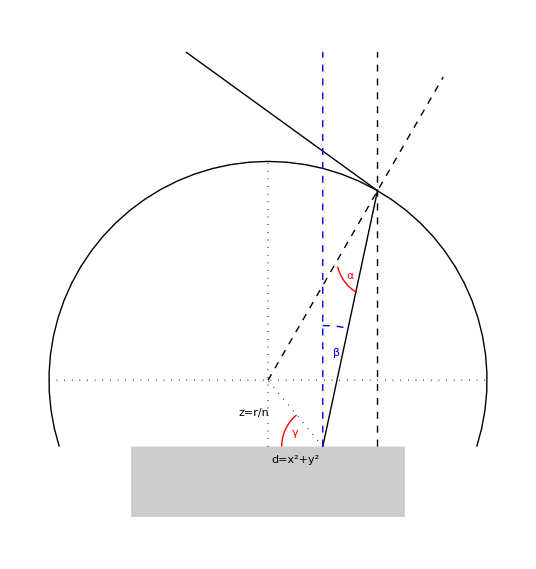

```mathematica
radius=0.8;
omega = Pi/3; (* angular position where ray hits the surface of the lens *)
xE = 0.2; (* x position of ray leaving the device *)
yD = -radius/nLens;(* y position of the device *)
Graphics[{Black,Circle[{0,0},radius,{-ArcSin[1/nLens],Pi+ArcSin[1/nLens]}],Opacity[0.2],Rectangle[{-0.5,-0.5},{0.5,yD }],Opacity[1],Line[{{xE,yD},{Cos[omega] radius,Sin[omega]radius}}],Line[{{Cos[omega] radius,Sin[omega]radius},{-0.3,1.2}}],Text["z=r/n",{-0.05,yD/2}],Text["d=x^2+y^2",{xE/2,yD-0.05}],Red,Circle[{(Cos[omega] radius+xE)/1.5,(Sin[omega]radius+yD)/1.5+0.15},0.15,{-3.7 Pi/4,-Pi/1.5}],Text["α",{xE+0.1,0.38}],Circle[{xE,yD},0.15,{-Pi,- Pi+ArcTan[yD/xE]}],Text["γ",{xE-0.1,yD+0.05}],Black,Dashed,Line[{{0,0},{1.6 Cos[omega] radius,1.6Sin[omega]radius}}],Dotted,Line[{{0,yD},{0,0.8}}],Line[{{-0.8,0},{+0.8,0.}}],Line[{{xE,yD},{0,0}}],Dashed,Line[{{Cos[omega] radius,yD},{Cos[omega] radius,1.2}}],Blue,Line[{{xE,yD},{xE,1.2}}],Text["β",{xE+0.05,0.1}],Circle[{xE,yD},-yD+0.2,{Pi/2,Pi/2-Pi/16}]}]
```

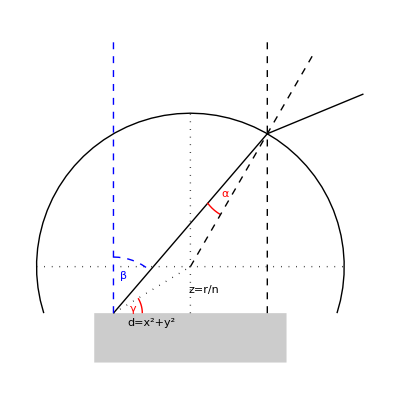

```mathematica
radius=0.8;
omega = Pi/3; (* angular position where ray hits the surface of the lens *)
xE = -0.4; (* x position of ray leaving the device *)
yD = -radius/nLens;(* y position of the device *)
Graphics[{Black,Circle[{0,0},radius,{-ArcSin[1/nLens],Pi+ArcSin[1/nLens]}],Opacity[0.2],Rectangle[{-0.5,-0.5},{0.5,yD }],Opacity[1],Line[{{xE,yD},{Cos[omega] radius,Sin[omega]radius}}],Line[{{Cos[omega] radius,Sin[omega]radius},{0.9,0.9}}],Text["z=r/n",{0.07,yD/2}],Text["d=x^2+y^2",{xE/2,yD-0.05}],Red,Circle[{(Cos[omega] radius)/1.5,(Sin[omega]radius)/1.5},0.22,{-Pi/1.25,-Pi/1.5}],Text["α",{xE+0.58,0.38}],Circle[{xE,yD},0.15,{0,ArcTan[yD/xE]}],Text["γ",{xE+0.1,yD+0.02}],Black,Dashed,Line[{{0,0},{1.6 Cos[omega] radius,1.6Sin[omega]radius}}],Dotted,Line[{{0,yD},{0,0.8}}],Line[{{-0.8,0},{+0.8,0.}}],Line[{{xE,yD},{0,0}}],Dashed,Line[{{Cos[omega] radius,yD},{Cos[omega] radius,1.2}}],Blue,Line[{{xE,yD},{xE,1.2}}],Text["β",{xE+0.05,-0.05}],Circle[{xE,yD},-yD+0.05,{Pi/2,Pi/2-Pi/4.5}]}]
```

Second step : integrate over it with the Planck radiation law, taking into account the probability of photons leaving through the lens, to get short circuit currents

```mathematica
nLens = 3.3;
radius = 0.8;
yD = -radius/nLens;(* y position of the device *)
zFun[xE1_,beta1_] := z/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE1; (* z-coordinate of point where the ray hits the lens *)
xFun[xE1_,beta1_] := emittedRayX[z]/.zsol/.beta->beta1/.r->radius/.n->nLens/.d->xE1; (*x-coordinate of point where the ray hits the lens *)
rayVec[xE_,beta_]:= {xFun[xE,beta]-xE,zFun[xE,beta]-yD};
radVec[xE_,beta_]:={xFun[xE,beta],zFun[xE,beta]};
alphaAbsFun[xE_,beta1_] := ArcCos[(rayVec[xE,beta1].radVec[xE,beta1])/Sqrt[(rayVec[xE,beta1].rayVec[xE,beta1]radVec[xE,beta1].radVec[xE,beta1])]];
alphaFun[xE_,beta1_]:= alphaAbsFun[xE,beta1] HeavisideTheta[Pi/2-beta1 - ArcTan[yD/xE]]UnitStep[-xE]-alphaAbsFun[xE,beta1]HeavisideTheta[-Pi/2+beta1 + ArcTan[yD/xE]]UnitStep[-xE]-alphaAbsFun[xE,beta1]UnitStep[xE];
alphaOutFun[xE_,beta1_] := ArcSin[nLens Sin[alphaFun[xE,beta1]]];
cetaFun[xE_,beta1_] :=HeavisideTheta[zFun[xE,beta1]]ArcTan[xFun[xE,beta1]/zFun[xE,beta1]]+HeavisideTheta[-zFun[xE,beta1]](Pi+ArcTan[xFun[xE,beta1]/zFun[xE,beta1]]);
outAngleFun[xE_,beta1_]:=alphaOutFun[xE,beta1]+cetaFun[xE,beta1];
```

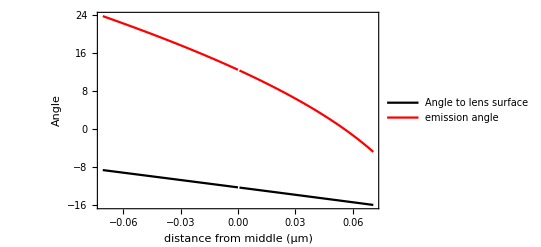

```mathematica
(* sanity check *)
Plot[{alphaFun[d,Pi/4]180/Pi,outAngleFun[d,Pi/4]180/Pi},{d,-Sqrt[2]0.05,Sqrt[2]0.05},PlotRange->All,PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Angle",""},{"distance from middle (μm)","β=45"}},PlotLegends->Placed[LineLegend[{"Angle to lens surface","emission angle"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.76,0.8}]]
```

```mathematica
reflSpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1]/.x->0.1/.y->0.2/.beta->0.1
reflPpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1]/.x->0/.y->0/.beta->0
```

1.

0.286101

```mathematica
nbeta = 120;
ndist = 100;
betas = Table[i Pi/(2 nbeta),{i,0,nbeta-1},{j,-ndist,ndist}];
dists = Table[i  Sqrt[2 0.05^2]/ndist,{j,0,nbeta-1},{i,-ndist,ndist}];
pescape = Table[0,{i,1,nbeta},{j,-ndist,ndist}];
For[i=1,i≤(nbeta),i++,
For[j=1,j≤(2ndist+1),j++,
beta = betas[[i]][[j]];
d = dists[[i]][[j]];
pescape[[i]][[j]] =Simplify[(2-reflSpol[alphaAbsFun[d,beta],nLens,1]-reflPpol[alphaAbsFun[d,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[d,beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) UnitStep[17.5 Pi/180 -Abs[outAngleFun[d,beta]]]];
]
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

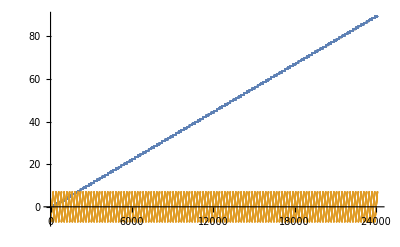

```mathematica
ListPlot[{Flatten[betas 180/Pi],100 Flatten[dists]}]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","pescape.csv"}],{Flatten[pescape],Flatten[betas 180/Pi]//N,Flatten[dists]//N}](*,betas,dists}*)
```

C:\Users\z3524693\Dropbox\Thermoradiative diode\Calculations\pescape.csv

```mathematica
ListPlot3D[pescape]
```

-Graphics3D-

```mathematica
Plot3D[(2-reflSpol[alphaAbsFun[d,beta],nLens,1]-refl   cvn23Ppol[alphaAbsFun[d,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[d,beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 -Abs[outAngleFun[d,beta]]],{beta,0,Pi/2},{d,-Sqrt[2 0.05^2],Sqrt[2 0.05^2]},PerformanceGoal->"Quality"]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* calculating the probability for light emitted from the active area into the lens to be emitted into the emission window of the device *)
(NIntegrate[Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*),{beta,0,Pi/2},{x,0,0.05},{y,0,0.05}]+(* also calculate in the negative direction *)NIntegrate[Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*),{beta,0,Pi/2},{x,0,0.05},{y,0,0.05}]
)/2/ Integrate[Sin[beta]Cos[beta],{beta,0,Pi/2},{x,0,0.05},{y,0,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000764491 and 1.56082×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000374158 and 3.78785×10^-6 for the integral and error estimates.

0.45546

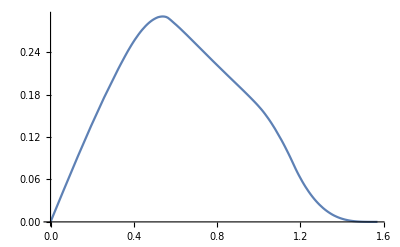

```mathematica
Plot[(NIntegrate[Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*),{x,0,0.05},{y,0,0.05}]+(* also calculate in the negative direction *)NIntegrate[Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*),{x,0,0.05},{y,0,0.05}]
)/2/ 0.05/0.05,{beta,0,Pi/2},PerformanceGoal->"Speed"]
```

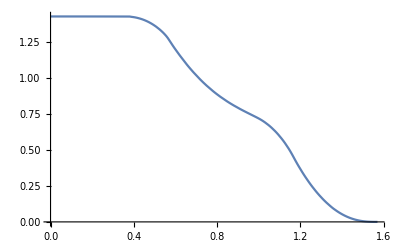

```mathematica
Plot[(NIntegrate[(2-reflSpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*),{x,0,0.05},{y,0,0.05}]+(* also calculate in the negative direction *)NIntegrate[(2-reflSpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*),{x,0,0.05},{y,0,0.05}]
)/ 0.05/0.05,{beta,0,Pi/2},PerformanceGoal->"Speed"]
```

```mathematica
52 Pi/180//N
```

0.907571

```mathematica
(NIntegrate[Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*)/.beta->Pi/4,{x,0,0.05},{y,0,0.05}]+(* also calculate in the negative direction *)NIntegrate[Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1]-reflPpol[alphaAbsFun[-Sqrt[x^2+y^2],beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-Sqrt[x^2+y^2],beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-Sqrt[x^2+y^2],beta]]](* angle of emission within angle of acceptance?*)/.beta->Pi/4,{x,0,0.05},{y,0,0.05}]
)
```

0.00112919

```mathematica
(* calculating the probability for light emitted from the active area into the lens to be emitted into the emission window of the device *)
(NIntegrate[Pi/2 rho Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]](* angle of emission within angle of acceptance?*),{beta,0,Pi/2},{rho,0,0.05}]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]](* angle of emission within angle of acceptance?*),{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05}]+(* also calculate in the negative direction *)NIntegrate[Pi/2 rho Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]](* angle of emission within angle of acceptance?*),{beta,0,Pi/2},{rho,0,0.05}]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]](* is the angle of incidence on the hyperhemisphere within the total internal reflection angle *) HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]](* angle of emission within angle of acceptance?*),{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05}]
)/2/ Integrate[Sin[beta]Cos[beta],{beta,0,Pi/2},{x,0,0.05},{y,0,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000329724 and 3.29021×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000449241 and 2.18443×10^-9 for the integral and error estimates.

0.455682

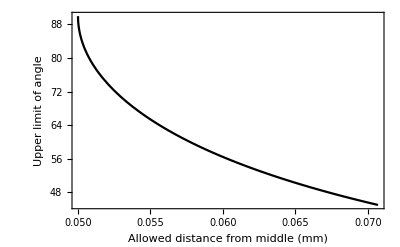

```mathematica
Plot[180/Pi ArcSin[1/20/rho],{rho,0.05,Sqrt[2]0.05},PlotStyle->{Black},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Upper limit of angle",""},{"Allowed distance from middle (mm)",""}}]
```

```mathematica
(* integral to determine the area outside the circle of radius a but inside the square with side-length a *)
NIntegrate[Integrate[2 rho,{theta,Pi/4,ArcSin[1/(2rho)]}],{rho,0.5,Sqrt[0.5]}]
```

0.0536505

```mathematica
Integrate[2 rho,{theta,Pi/4,ArcSin[1/(2rho)]}]
```

2 rho (-π/4+ArcSin[1/(2 rho)])

```mathematica
(* transforming 2D area integral into 1D integral *)
Integrate[2 rho Pi/4,{rho,0,0.5}]+0.053650459150637986
```

0.25

The terms involved in the emission integral

Pi/2 ρ and 2 ρ (-π/4+ArcSin[1/(20 ρ)]), respectively are due to the transformation of the emission integral from x,y coordinates into ρ,θ and subsequent integration over θ

Sin[β]Cos[β] is due to the angular integral

(1-Exp[Log[1-eqeFun[E]/0.714]/(Cos[β])]) calculates the angular dependence of the absorptivity of the device for light that’s already inside the lens [0.714 is (1-R(0)) and transforms EQE for free space light into IQE]

E^2 (n_Lens^2 prefac)/(Exp[E/T]-1) is the optical DOS and the Planck distribution of photons

(2-reflSpol[alphaAbsFun[ρ,β],n_Lens,1]-reflPpol[alphaAbsFun[ρ,β],n_Lens,1])/2 is the average of the reflectivity at the surface of the lens

HeavisideTheta[1 -n_Lens Abs[Sin[alphaFun[ρ,β]]]] represents total internal reflection in the lens

HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[ρ,β]]] ensures that only light in the acceptance angle is counted

```mathematica
(* calculating the amount of light emitted from the acceptance angle of the device at a particular temperature *)
2 (* the four integrals represent 2 quadrants of the rectangle in the x-y-plane, so I need a factor of 2 to account for the other 2 quadrants *)(NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/Exp[(energy)/Tcell](2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]]  HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},{energy,Min[energy6],Max[energy6]}]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/Exp[(energy)/Tcell](2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},{energy,Min[energy6],Max[energy6]}]+NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/Exp[(energy)/Tcell](2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},{energy,Min[energy6],Max[energy6]}]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/Exp[(energy)/Tcell](2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},{energy,Min[energy6],Max[energy6]}]
)
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.35111 and 0.0000701208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0788429 and 0.0000108445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.163119 and 0.00126616 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1.22743

```mathematica
2(* normalisation due to Sin(x) Cos(x) integral *)  1.2276556851454938(* microAmp calculated by integrating over spectrum (300K)*)/10^6/emittedLight6[300Tcell/300/.constants,0](* emitted photon flux assuming angle-independent EQE *)
```

1.

```mathematica
Integrate[Sin[x]Cos[x],{x,0,Pi/2}]
```

1/2

```mathematica
(* testing that my conversion of EQEfun is correct *)
1-Exp[Log[1-eqeFun5[Min[energy5]]/0.714]/(Cos[0])]
eqeFun5[Min[energy5]]/0.714
```

0.004146

0.004146

## Calculating the current

### old analytic approach

```mathematica
(* calculating the amount of light emitted from the acceptance angle of the device at a particular temperature *)
emittedCurrenteqe6[T_]:=4(NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]]  HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},{energy,Min[energy6],Max[energy6]},AccuracyGoal->6]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},{energy,Min[energy6],Max[energy6]},AccuracyGoal->6]+NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},{energy,Min[energy6],Max[energy6]},AccuracyGoal->6]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},{energy,Min[energy6],Max[energy6]},AccuracyGoal->6]
);
(* calculating the amount of light emitted from the acceptance angle of the device at a particular temperature *)
emittedCurrenteqe10[T_]:=4(NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun10[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]]  HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},{energy,Min[energy10],Max[energy10]},AccuracyGoal->6]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun10[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},{energy,Min[energy10],Max[energy10]},AccuracyGoal->6]+NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun10[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},{energy,Min[energy10],Max[energy10]},AccuracyGoal->6]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun10[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)(2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},{energy,Min[energy10],Max[energy10]},AccuracyGoal->6]
);
```

### Using the data from ray tracing

```mathematica
(* read in data for escape probability as function of emission angle *)
rayTraceData= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","hyperhemi_T_withinangle_u.txt"}],"Data"];
rTdatAngle =  Transpose[rayTraceData][[1]];
rTdatEscape = Transpose[rayTraceData][[2]];
rayTraceData45= Import[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","hyperhemi_T_withinangle_u_45.txt"}],"Data"];
rTdatAngle45 =  Transpose[rayTraceData45][[1]];
rTdatEscape45 = Transpose[rayTraceData45][[2]];
rayTraceEscapeFun=Interpolation[Transpose[{rTdatAngle,rTdatEscape}]] ;
rayTraceEscapeFun45=Interpolation[Transpose[{rTdatAngle45,rTdatEscape45}]] ;
(*rayTraceEscapeFunMax=Interpolation[Transpose[{rTdatAngle,rTdatTotEscape}]] ;*)
```

```mathematica
Max[rTdatAngle45] 180/Pi
```

87.1352110243458779

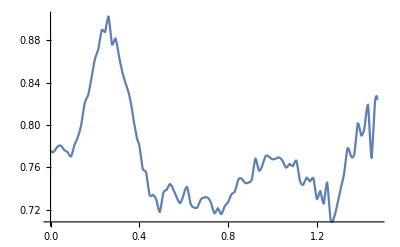

```mathematica
Plot[rayTraceEscapeFun45[x],{x,0,Max[rTdatAngle]}]
```

```mathematica
(* calculating the amount of light emitted from the acceptance angle of the device at a particular temperature *)
emittedCurrentRayTraceeqe6[T_]:=2 NIntegrate[rayTraceEscapeFun[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle]},{energy,Min[energy6],Max[energy6]}];
emittedCurrentRayTrace45eqe6[T_]:=2 NIntegrate[rayTraceEscapeFun45[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle45]},{energy,Min[energy6],Max[energy6]}];
emittedCurrentRayTraceMaxeqe6[T_]:=2 NIntegrate[rayTraceEscapeFunMax[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle]},{energy,Min[energy6],Max[energy6]}];
(* calculating the amount of light emitted from the acceptance angle of the device at a particular temperature *)
emittedCurrentRayTraceeqe5[T_]:=2 NIntegrate[rayTraceEscapeFun[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun5[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle]},{energy,Min[energy5],Max[energy5]}];
emittedCurrentRayTrace45eqe5[T_]:=2 NIntegrate[rayTraceEscapeFun45[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun5[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle45]},{energy,Min[energy5],Max[energy5]}];
emittedCurrentRayTraceMaxeqe5[T_]:=2 NIntegrate[rayTraceEscapeFunMax[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun5[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle]},{energy,Min[energy5],Max[energy5]}];
(* calculating the amount of light emitted from the acceptance angle of the device at a particular temperature *)
emittedCurrentRayTraceeqe4[T_]:=2 NIntegrate[rayTraceEscapeFun[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun4[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle]},{energy,Min[energy4],Max[energy4]}];
emittedCurrentRayTrace45eqe4[T_]:=2 NIntegrate[rayTraceEscapeFun45[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun4[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle45]},{energy,Min[energy4],Max[energy4]}];
emittedCurrentRayTraceMaxeqe4[T_]:=2 NIntegrate[rayTraceEscapeFunMax[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun4[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle]},{energy,Min[energy4],Max[energy4]}];
emittedCurrentRayTrace45eqe10[T_]:=2 NIntegrate[rayTraceEscapeFun45[beta]Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun10[energy]/0.714]/(Cos[beta])])energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle45]},{energy,Min[energy10],Max[energy10]}];
```

```mathematica
emittedCurrentRayTraceeqe6[293.3 Tcell/300 /.constants] 0.1^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 117.647 and 0.00183837 for the integral and error estimates.

2.35294

```mathematica
emittedCurrenteqe6[293Tcell/300]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.282234 and 0.0000560729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0633347 and 8.51912×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.130952 and 0.00101567 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1.97234

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","currentVsTemperature6micronDetector.csv"}],{currents,temps}];
```

/Users/andreaspusch/Dropbox/Thermoradiative diode/Calculations/currentVsTemperature6micronDetector.csv

```mathematica
emittedCurrentRayTrace45eqe4Normal[T_]:=2 NIntegrate[rayTraceEscapeFun45[beta]Sin[beta]Cos[beta]eqeFun4[energy]/0.714 energy^2 (nLens^2 prefac)/(Exp[(energy)/T]-1)/.constants,{beta,0,Max[rTdatAngle45]},{energy,Min[energy4],Max[energy4]}];
```

```mathematica
emittedCurrentRayTrace45eqe4Normal[0.026]/emittedCurrentRayTrace45eqe4[0.026]
```

0.762173

### The actual calculation

```mathematica
temps = Table[i,{i,0,50}];
currentDiode6 = 0.01 emittedCurrentRayTraceeqe6[(293.45)Tcell/300];
currentDiode6Max =  0.01 emittedCurrentRayTraceMaxeqe6[(293.45)Tcell/300];
currentsSimple = Table[0,Length[temps]];
currentsRayTrace = Table[0,Length[temps]];
currentsRayTraceMax = Table[0,Length[temps]];
For[i=1,i≤Length[temps],i++,
currentsSimple[[i]]=emittedLight6[(temps[[i]]+273.15)Tcell/300,0] 10^6;
currentsRayTrace[[i]] =0.01 emittedCurrentRayTraceeqe6[(temps[[i]]+273.15)Tcell/300];
currentsRayTraceMax[[i]] =0.01emittedCurrentRayTraceMaxeqe6[(temps[[i]]+273.15)Tcell/300];

]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.21 and 0.00184711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 59.3306 and 0.000914176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 98.5143 and 0.000850749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 61.5122 and 0.000952663 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","approxCurrentVsT6mu.csv"}],{currentsSimple,temps}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracedCurrentVsT6mu.csv"}],{currentsRayTrace-currentDiode6,temps}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracedMaxCurrentVsT6mu.csv"}],{currentsRayTraceMax-currentDiode6Max,temps}];
```

```mathematica
temps = Table[i,{i,0,50}];
currentDiode645 = 0.01 emittedCurrentRayTrace45eqe6[(293.65)Tcell/300];
currentDiode545 =  0.01 emittedCurrentRayTrace45eqe5[(293.65)Tcell/300];
currentDiode445 =  0.01 emittedCurrentRayTrace45eqe4[(293.65)Tcell/300];
currentsRayTrace645 = Table[0,Length[temps]];
currentsRayTrace545 = Table[0,Length[temps]];
currentsRayTrace445 = Table[0,Length[temps]];
For[i=1,i≤Length[temps],i++,
currentsRayTrace645[[i]]=0.01 emittedCurrentRayTrace45eqe6[(temps[[i]]+273.15)Tcell/300];
currentsRayTrace545[[i]] =0.01 emittedCurrentRayTrace45eqe5[(temps[[i]]+273.15)Tcell/300];
currentsRayTrace445[[i]] =0.01emittedCurrentRayTrace45eqe4[(temps[[i]]+273.15)Tcell/300];

]
```

```mathematica
currentsRayTrace645
```

{1.90432,1.97388,2.0455,2.11923,2.1951,2.27317,2.35348,2.43609,2.52104,2.60838,2.69815,2.79042,2.88523,2.98263,3.08268,3.18543,3.29093,3.39923,3.5104,3.62448,3.74153,3.86161,3.98478,4.1111,4.24061,4.37339,4.50949,4.64898,4.7919,4.93833,5.08833,5.24196,5.39928,5.56029,5.72519,5.89404,6.06679,6.24355,6.42439,6.6094,6.79862,6.99214,7.19002,7.39233,7.59914,7.81052,8.02656,8.2473,8.47284,8.70325,8.93859}

```mathematica
currentDiode645 = 0.01 emittedCurrentRayTrace45eqe6[(293.65)Tcell/300];
currentDiode545 =  0.01 emittedCurrentRayTrace45eqe5[(293.65)Tcell/300];
currentDiode445 =  0.01 emittedCurrentRayTrace45eqe4[(293.65)Tcell/300];
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","rayTraced45CurrentVsT6mu.csv"}],{currentsRayTrace645-currentDiode645,temps}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","rayTraced45CurrentVsT5mu.csv"}],{currentsRayTrace545-currentDiode545,temps}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","rayTraced45CurrentVsT4mu.csv"}],{currentsRayTrace445-currentDiode445,temps}];
```

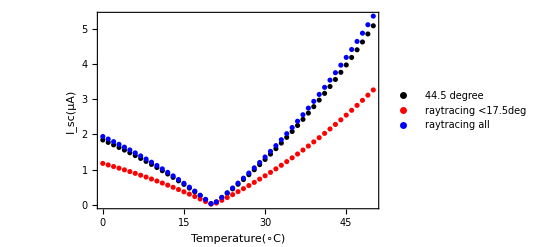

```mathematica
ListPlot[{Transpose[{temps,Abs[currentsRayTrace645-currentDiode645] }],Transpose[{temps,Abs[currentsRayTrace- currentDiode6]}],Transpose[{temps,Abs[currentsRayTraceMax-currentDiode6Max] }]},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I_sc(μA)",""},{"Temperature(∘C)","T_D=293.45 K"}},PlotLegends->Placed[LineLegend[{"44.5 degree","raytracing <17.5deg","raytracing all"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.5,0.8}]]
```

```mathematica
temps = Table[i,{i,0,50}];
currentDiode5Max = 0.01 emittedCurrentRayTraceMaxeqe5[(293.45)Tcell/300];
currentDiode5 = 0.01 emittedCurrentRayTraceeqe5[(293.45)Tcell/300];
currentsRayTrace5 = Table[0,Length[temps]];
currentsRayTraceMax5 = Table[0,Length[temps]];
For[i=1,i≤Length[temps],i++,
currentsRayTrace5[[i]] =0.01 emittedCurrentRayTraceeqe5[(temps[[i]]+273.15)Tcell/300];
currentsRayTraceMax5[[i]] =0.01emittedCurrentRayTraceMaxeqe5[(temps[[i]]+273.15)Tcell/300];

]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 66.4863 and 0.00193986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 40.5717 and 0.00179986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18.2995 and 0.00074878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 30.1027 and 0.000814446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.0798 and 0.000789447 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
temps = Table[i,{i,0,50}];
currentDiode4Max = 0.01 emittedCurrentRayTraceMaxeqe4[(293.45)Tcell/300];
currentDiode4 = 0.01 emittedCurrentRayTraceeqe4[(293.45)Tcell/300];
currentsRayTrace4 = Table[0,Length[temps]];
currentsRayTraceMax4 = Table[0,Length[temps]];
For[i=1,i≤Length[temps],i++,
currentsRayTrace4[[i]] =0.01 emittedCurrentRayTraceeqe4[(temps[[i]]+273.15)Tcell/300];
currentsRayTraceMax4[[i]] =0.01emittedCurrentRayTraceMaxeqe4[(temps[[i]]+273.15)Tcell/300];

]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18.9551 and 0.000306207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.6139 and 0.000355029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.67697 and 0.000142948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.66068 and 0.000117539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.90569 and 0.000149219 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracedCurrentVsT5mu.csv"}],{currentsRayTrace5-currentDiode5,temps}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracedMaxCurrentVsT5mu.csv"}],{currentsRayTraceMax5-currentDiode5Max,temps}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracedCurrentVsT4mu.csv"}],{currentsRayTrace4-currentDiode4,temps}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracedMaxCurrentVsT4mu.csv"}],{currentsRayTraceMax4-currentDiode4Max,temps}];
```

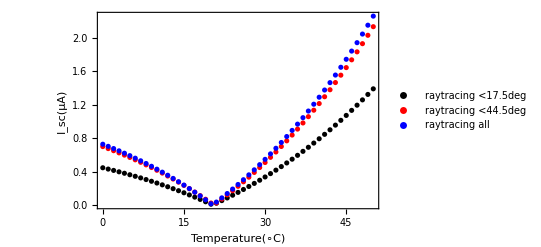

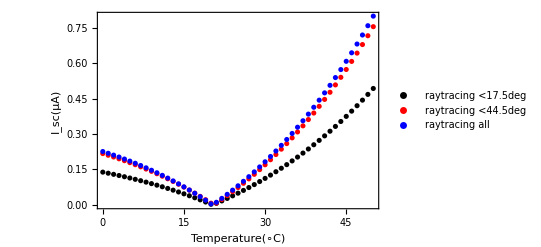

```mathematica
ListPlot[{Transpose[{temps,Abs[currentsRayTrace5- currentDiode5]}],Transpose[{temps,Abs[currentsRayTrace545- currentDiode545]}],Transpose[{temps,Abs[currentsRayTraceMax5-currentDiode5Max] }]},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I_sc(μA)",""},{"Temperature(∘C)","T_D=293.65 K, 5μm"}},PlotLegends->Placed[LineLegend[{"raytracing <17.5deg","raytracing <44.5deg","raytracing all"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.5,0.8}]]
ListPlot[{Transpose[{temps,Abs[currentsRayTrace4- currentDiode4]}],Transpose[{temps,Abs[currentsRayTrace445- currentDiode445]}],Transpose[{temps,Abs[currentsRayTraceMax4-currentDiode4Max] }]},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I_sc(μA)",""},{"Temperature(∘C)","T_D=293.65 K, 4μm"}},PlotLegends->Placed[LineLegend[{"raytracing <17.5deg","raytracing <44.5deg","raytracing all"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.5,0.8}]]
```

```mathematica
2 Sqrt[2]//N
```

2.82843

## Calculation of EL (Probably not TODO: should probably be modified for the ray tracing results and include the other diodes)

```mathematica
EL6precise = Table[0,Length[wl6]];
For[i=1,i≤ Length[wl6],i++,EL6precise[[i]] = 4(NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[2 Pi hbar clight 10^6/echarge/wl6[[i]]]/0.714]/(Cos[beta])]) (2 Pi hbar clight 10^6/echarge/wl6[[i]])^4(nLens^2 prefac)/(Exp[(2 Pi hbar clight 10^6/echarge/wl6[[i]])/(293Tcell/300)]-1)(2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]]  HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},PrecisionGoal->3]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[2 Pi hbar clight 10^6/echarge/wl6[[i]]]/0.714]/(Cos[beta])])(2 Pi hbar clight 10^6/echarge/wl6[[i]])^4 (nLens^2 prefac)/(Exp[(2 Pi hbar clight 10^6/echarge/wl6[[i]])/(293Tcell/300)]-1)(2-reflSpol[alphaAbsFun[rho,beta],nLens,1]-reflPpol[alphaAbsFun[rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},PrecisionGoal->3]+NIntegrate[Pi/2 rho Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[2 Pi hbar clight 10^6/echarge/wl6[[i]]]/0.714]/(Cos[beta])])(2 Pi hbar clight 10^6/echarge/wl6[[i]])^4 (nLens^2 prefac)/(Exp[(2 Pi hbar clight 10^6/echarge/wl6[[i]])/(293Tcell/300)]-1)(2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0,0.05},PrecisionGoal->3]+NIntegrate[2 rho (-π/4+ArcSin[1/(20 rho)]) Sin[beta]Cos[beta](1-Exp[Log[1-eqeFun[2 Pi hbar clight 10^6/echarge/wl6[[i]]]/0.714]/(Cos[beta])])(2 Pi hbar clight 10^6/echarge/wl6[[i]])^4 (nLens^2 prefac)/(Exp[(2 Pi hbar clight 10^6/echarge/wl6[[i]])/(293Tcell/300)]-1)(2-reflSpol[alphaAbsFun[-rho,beta],nLens,1]-reflPpol[alphaAbsFun[-rho,beta],nLens,1])/2HeavisideTheta[1 -nLens Abs[Sin[alphaFun[-rho,beta]]]] HeavisideTheta[17.5 Pi/180 - Abs[outAngleFun[-rho,beta]]]/.constants,{beta,0,Pi/2},{rho,0.05,Sqrt[2]0.05},PrecisionGoal->3]
);]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
EL6
```

{9.17842×10^-7,1.31667×10^-6,2.37419×10^-6,3.49792×10^-6,0.0000240839,0.000111918,0.000337544,0.000678873,0.00104949,0.00146052,0.00194476,0.00269935,0.00320652,0.00385114,0.00474693,0.00635613,0.00822937,0.0101498,0.0126453,0.0159651,0.0197313,0.0256993,0.0355796,0.0495114,0.067901,0.0906969,0.118921,0.154545,0.196465,0.24737,0.307577,0.377928,0.458557,0.55429,0.659389,0.777295,0.914533,1.06591,1.22667,1.40324,1.60671,1.81472,2.03498,2.27276,2.51851,2.77001,3.02368,3.27779,3.53037,3.74605,3.95166,4.10691,4.17204,4.22455,4.23772,4.22613,4.20871,4.13974,4.06444,3.96919,3.87776,3.71231,3.58119,3.48456,3.32931,3.19164,3.01223,2.84756,2.65188,2.46744,2.25033,2.09565,1.88672,1.69012,1.49355,1.28576,1.11465,0.894527,0.728485,0.541231,0.424631,0.35172,0.227569,0.180724,0.119424,0.0673101}

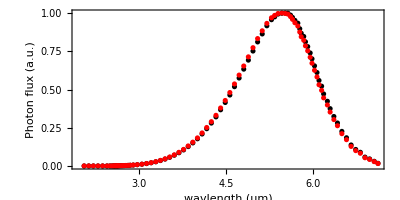

```mathematica
(* EL spectrum calculated with the angle dependence included *)
ListPlot[{Transpose[{wl6,EL6precise/Max[EL6precise]}],Transpose[{wl6,EL6/Max[EL6]}]},AspectRatio->1/2,PlotStyle->{Black,Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"Photon flux (a.u.)",""},{"wavlength (μm)","EL spectrum of diode from EQE"}},PerformanceGoal->"Speed"]
```

```mathematica
(* emission for a planar surface into a hemisphere *)
emittedLight6planar[T_,mu_] := NIntegrate[ energy^2 (prefac eqeFun[energy])/((2-reflSpol[0,nLens,1]-reflPpol[0,nLens,1])/2(* converting EQE to IQE to get the emissivity of the diode surface *)(Exp[(energy-mu)/T]-1))/.constants,{energy,Min[energy6],Max[energy6]},PrecisionGoal->6] ;
emittedLight5planar[T_,mu_] := NIntegrate[ energy^2 (prefac eqeFun5[energy])/((2-reflSpol[0,nLens,1]-reflPpol[0,nLens,1])/2(* converting EQE to IQE to get the emissivity of the diode surface *)(Exp[(energy-mu)/T]-1))/.constants,{energy,Min[energy5],Max[energy5]},PrecisionGoal->6] ;
emittedLight4planar[T_,mu_] := NIntegrate[ energy^2 (prefac eqeFun4[energy])/((2-reflSpol[0,nLens,1]-reflPpol[0,nLens,1])/2(* converting EQE to IQE to get the emissivity of the diode surface *)(Exp[(energy-mu)/T]-1))/.constants,{energy,Min[energy4],Max[energy4]},PrecisionGoal->6] ;
thetaDiode = Pi/180 17.5 (* half angle of acceptance *);
emittedLight6[T_,mu_] :=2.59407/2 0.9486423778113563 (* this is an approximation that assumes that a small change in temperature doesn't do much to the frequency distribution of the emission *) emittedLight6planar[T,mu] nLens^2 0.45545957976535084(* see calculation of escape probability above *) 10^-8 (* area of diode *);
(emittedLight6[293Tcell/300/.constants,0]-emittedLight6[286 Tcell/300/.constants,0])
```

4.04995×10^-7

```mathematica
emittedLight6[293Tcell/300/.constants,0]/.constants
```

1.96937×10^-6

## Double checking the power calculations

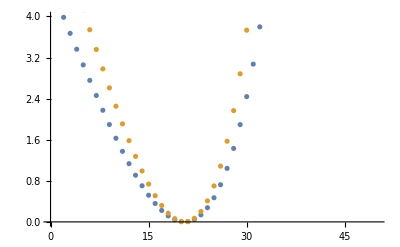

```mathematica
ListPlot[{Transpose[{temps,(currentsRayTrace545-currentDiode545)^2 res5 /4 0.1 }],Transpose[{temps,(currentsRayTrace445-currentDiode445)^2 res4 /4 0.11 }]},PlotRange->{0,4}]
```

```mathematica
currentDiode445 res4 /4  0.01
```

4.25983

## Hypothetical powers for the diodes against a 3K background from the ray tracing results for 44.5 degrees

```mathematica
(* total short circuit currents *)
Isc5 =10^-6 emittedCurrentRayTrace45eqe5[293 Tcell/300 /.constants] 0.1^2
Isc6 = 10^-6 emittedCurrentRayTrace45eqe6[293  Tcell/300 /.constants] 0.1^2
Isc4 =10^-6 emittedCurrentRayTrace45eqe4[293 Tcell/300 /.constants] 0.1^2
Isc10 =10^-6 emittedCurrentRayTrace45eqe10[293 Tcell/300 /.constants] 0.1^2
```

1.261×10^-6

3.72378×10^-6

3.58361×10^-7

0.0000193452

```mathematica
(* total powers from I_sc V_oc/4 = I_sc^2 V_oc / 4 *)
res6 = 56;
res5 = 377;
res4 = 4700;
res10 = 2.49;
P6tot = res6 Isc6^2/4;
P5tot = res5 Isc5^2/4;
 P4tot = res4 Isc4^2/4;
P10tot = res10 Isc10^2/4;
(* power density by normalising to the area of (0.1mm)^2 of the diodes *)
P6dens = P6tot 10^8
P5dens = P5tot 10^8
P4dens = P4tot 10^8
P10dens = P10tot 10^8
```

0.0194132

0.0149869

0.0150896

0.0232962

```mathematica
Isc40C = Isc4 -  10^-6 emittedCurrentRayTrace45eqe4[273.15 Tcell/300 /.constants] 0.1^2
Isc50C = Isc5 -  10^-6 emittedCurrentRayTrace45eqe5[273.15 Tcell/300 /.constants] 0.1^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.26666 and 0.0000944045 for the integral and error estimates.

2.07495×10^-7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 28.5616 and 0.000597656 for the integral and error estimates.

6.69549×10^-7

```mathematica
Isc4m20C = Isc4 -  10^-6 emittedCurrentRayTrace45eqe4[253.15 Tcell/300 /.constants] 0.1^2
Isc5m20C = Isc5 -  10^-6 emittedCurrentRayTrace45eqe5[253.15 Tcell/300 /.constants] 0.1^2
Isc4m20C^2 res4/4 10^11
Isc5m20C^2 res5 /4 10^11
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.60852 and 0.0000337969 for the integral and error estimates.

3.00658×10^-7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.6808 and 0.000236026 for the integral and error estimates.

1.00716×10^-6

10.6215

9.56054

```mathematica
Isc4m50C = Isc4 -  10^-6 emittedCurrentRayTrace45eqe4[223.15 Tcell/300 /.constants] 0.1^2
Isc5m50C = Isc5 -  10^-6 emittedCurrentRayTrace45eqe5[223.15 Tcell/300 /.constants] 0.1^2
Isc4m50C^2 res4/4 10^11
Isc5m50C^2 res5 /4 10^11
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.407041 and 4.91612×10^-6 for the integral and error estimates.

3.44688×10^-7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3191 and 0.000043639 for the integral and error estimates.

1.1944×10^-6

13.9601

13.4456

```mathematica
Isc40C^2 res4/4 10^11
Isc50C^2 res5 /4 10^11 (* mW/m^2*)
```

5.05888

4.22518

## Powers for a large range of temperatures from dynamic resistance and ray tracing results

```mathematica
Flatten[{Table[0,2],Table[1,2]}]
```

{0,0,1,1}

```mathematica
(*tempsDR = {3,100,200,292};*)
tempsDR = Flatten[{Table[10 i,{i,100/10,200/10}],Table[2i,{i,101,293/2}]}]
currentsRay445293K = Table[0,Length[tempsDR]];
currentsRay545293K= Table[0,Length[tempsDR]];
currentsRay645293K =  Table[0,Length[tempsDR]];
currentsRay1045293K =  Table[0,Length[tempsDR]];
For[i=1,i≤Length[tempsDR],i++,
currentsRay445293K[[i]] =Isc4-10^-8 emittedCurrentRayTrace45eqe4[(tempsDR[[i]])Tcell/300];
currentsRay545293K[[i]] =Isc5-10^-8 emittedCurrentRayTrace45eqe5[(tempsDR[[i]])Tcell/300];
currentsRay645293K[[i]] =Isc6 -10^-8 emittedCurrentRayTrace45eqe6[(tempsDR[[i]])Tcell/300];
currentsRay1045293K[[i]] =Isc10-10^-8 emittedCurrentRayTrace45eqe10[(tempsDR[[i]])Tcell/300];
]
```

{100,110,120,130,140,150,160,170,180,190,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254,256,258,260,262,264,266,268,270,272,274,276,278,280,282,284,286,288,290,292}

14766

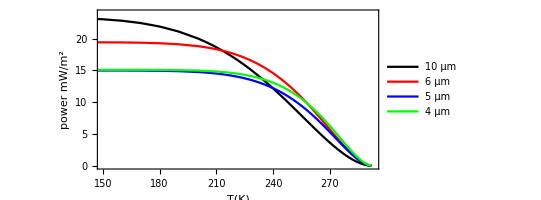

```mathematica
ListPlot[{Transpose[{tempsDR,10^11 currentsRay1045293K^2 res10/4}],Transpose[{tempsDR,10^11 currentsRay645293K^2 res6/4}],Transpose[{tempsDR,10^11 currentsRay545293K^2 res5/4}],Transpose[{tempsDR,10^11 currentsRay445293K^2 res4/4}]},AspectRatio->1/2,PlotStyle->{Black,Red,Blue,Green},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"power mW/m^2",""},{"T(K)","Theoretical T-dependence of power"}},PlotRange->{{150,293},{0,24}},Joined->True,PlotLegends->Placed[LineLegend[{"10 μm","6 μm","5 μm","4 μm"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.25,0.3}]]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","rayTracedCurrent293KVsT10mu.csv"}],{currentsRay1045293K,tempsDR}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","rayTracedCurrent293KVsT6mu.csv"}],{currentsRay645293K,tempsDR}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","rayTracedCurrent293KVsT5mu.csv"}],{currentsRay545293K,tempsDR}];
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","rayTracingResults","rayTracedCurrent293KVsT4mu.csv"}],{currentsRay445293K,tempsDR}];
```

## Determine non-radiative properties and assemble the I-V curve

TODO think again about how to calculate radiative efficiency by defining it as the number of electron hole pairs injected into the device at the maximum power point compared to the difference in photon flux.

### Radiative efficiency directly from the dynamic resistance and Isc

Change in current from dynamic resistance is due to nonradiative recombination/generation. The total non-radiative generation is obtained when the  negative voltage is much larger than the temperature.

I(V) = (Exp(-V/T) J0rad - Jabs) - (1-Exp(-nAug V/T)) J0Aug - (1-Exp(-nSRH V/T)) J0SRH

Set Jabs,J0rad=0 for this. ΔI(V) ≈ -(nAug*J0Aug+nSRH * J0SRH) V / T

ΔI/ΔV = 1/R = (nAug* J0Aug + nSRH * J0SRH)/T

```mathematica
J0nonrad6 = 293/300Tcell/res6/.constants ;
Isc6/J0nonrad6
J0nonrad5= 293/300Tcell/res5/.constants ;
Isc5/J0nonrad5
J0nonrad4= 293/300Tcell/res4/.constants ;
Isc4/J0nonrad4
```

0.00811812

0.0185266

0.0656782

### Radiative efficiencies from the Auger calculations

```mathematica
Isc6/(10^-8 jAugRogalski[293.15/300 Tcell,moleFracCd,8 10^-6,2 10^22,-1]+10^-8 jSRH[293.15/300 Tcell,10^-6,moleFracCd,8 10^-6,2 10^22,-1])/.constants //ScientificForm
Isc6
10^-8 jAugRogalski[293.15/300 Tcell,moleFracCd,8 10^-6,2 10^22,-1]/.constants//ScientificForm
10^-8 jSRH[293.15/300 Tcell,10^-6,moleFracCd,8 10^-6,2 10^22,-1]/.constants//ScientificForm
```

-5.57732×10^-3

3.66023×10^-6

-5.9202×10^-4

-6.42509×10^-5

```mathematica
Isc6 res6
Isc5 res5/(Isc4 res4)
```

0.000204973

0.282082

```mathematica
(* these values were established to obtain the correct dynamic resistance *)
Isc5/(10^-8 jAugRogalski[293.15/300 Tcell,0.27,18 10^-6,3 10^22,-1]+10^-8 jSRH[293.15/300 Tcell,10^-6,0.27,18 10^-6,3 10^22,-1])/.constants//ScientificForm
```

-5.62086×10^-3

```mathematica
Isc4/(10^-8 jAugRogalski[293.15/300 Tcell,0.315,15 10^-6,3 10^22,-1]+10^-8 jSRH[293.15/300 Tcell,10^-6,0.315,15 10^-6,3 10^22,-1])/.constants//ScientificForm
```

-2.18338×10^-2

```mathematica
562.086 / 2183.88//N
```

0.25738

```mathematica
(* equations 15 and 18 of Rogalski Review paper *)
j0Aug[T_,x_,thickness_,doping_]:= echarge thickness (ni[T,x,Egfun[x,T]]^2/(2 ni[T,x,Egfun[x,T]]^2)) (nReal[doping,T,x,Egfun[x,T],0]/((1+nReal[doping,T,x,Egfun[x,T],0]5.26 10^-24)tAuger[Egfun[x,T],T])+pReal[doping,T,x,Egfun[x,T],0]/(8 tAuger[Egfun[x,T],T]));
jAugRogalski[T_,x_,thickness_,doping_,voltage_]:= echarge thickness ((nReal[doping,T,x,Egfun[x,T],voltage] pReal[doping,T,x,Egfun[x,T],voltage]-ni[T,x,Egfun[x,T]]^2)/(2 ni[T,x,Egfun[x,T]]^2)) (nReal[doping,T,x,Egfun[x,T],voltage]/((1+nReal[doping,T,x,Egfun[x,T],voltage]5.26 10^-24)tAuger[Egfun[x,T],T])+pReal[doping,T,x,Egfun[x,T],voltage]/(8 tAuger[Egfun[x,T],T]));(*first part of equation (6) of Zhang2020*)
j0SRH[T_,tauSRH_,x_,thickness_,doping_]:=echarge (thickness/tauSRH)((nReal[doping,T,x,Egfun[x,T],0]pReal[doping,T,x,Egfun[x,T],0])/(nReal[doping,T,x,Egfun[x,T],0]+pReal[doping,T,x,Egfun[x,T],0] +2ni[T,x,Egfun[x,T]]));
jSRH[T_,tauSRH_,x_,thickness_,doping_,voltage_]:=echarge (thickness/tauSRH)((nReal[doping,T,x,Egfun[x,T],voltage]pReal[doping,T,x,Egfun[x,T],voltage]-ni[T,x,Egfun[x,T]]^2)/(nReal[doping,T,x,Egfun[x,T],voltage]+pReal[doping,T,x,Egfun[x,T],voltage] +2ni[T,x,Egfun[x,T]]));
```

```mathematica
moleFracCd = 0.23;(*x/.FindRoot[Egfun[x,Tcell]==2 Pi hbar clight 10^6/echarge/6/.constants,{x,0.2}]
Egfun[moleFracCd,293 Tcell/300]/.constants*)
ni[Tcell,moleFracCd,Egfun[moleFracCd,Tcell]]/.constants
tAug6 = tAuger[Egfun[moleFracCd,Tcell],Tcell]/.constants
tAuger[Egfun[moleFracCd,293Tcell/300],293Tcell/300]/.constants
current6[Tdiode_,Tenv_,voltage_,thickness_,tauSRH_] := -emittedLight6[Tdiode,voltage]+emittedLight6[Tenv,0]-10^-8(* actual active area of the device *)jSRH[Tdiode,tauSRH,moleFracCd,thickness,0,voltage]-10^-8 jAugRogalski[Tdiode,moleFracCd,thickness,0,voltage]; 
current6p[Tdiode_,Tenv_,voltage_,thickness_,tauSRH_,pdope_] := - emittedLight6[Tdiode,voltage]+ emittedLight6[Tenv,0]-10^-8(* actual active area of the device *)jSRH[Tdiode,tauSRH,moleFracCd,thickness,-pdope,voltage]-10^-8 jAugRogalski[Tdiode,moleFracCd,thickness,-pdope,voltage]; 
(* just for test purposes *)
current10p[Tdiode_,Tenv_,voltage_,thickness_,tauSRH_,pdope_] := - emittedLight6[Tdiode,voltage]+ emittedLight6[Tenv,0]-10^-8(* actual active area of the device *)jSRH[Tdiode,tauSRH,moleFrac10,thickness,-pdope,voltage]-10^-8 jAugRogalski[Tdiode,moleFrac10,thickness,-pdope,voltage];
```

1.77995×10^22

1.72316×10^-7

1.96458×10^-7

### Estimating the dynamic resistance at different temperatures

```mathematica
(* the 6 micron diode should be approximately 8. micron thick *)
res6p =10/Abs[10^6 (current6p[293Tcell/300/.constants,3 Tcell/300/.constants,-10/10^6,8. 10^-6,10^-6,2 10^22]-current6p[293Tcell/300/.constants,3 Tcell/300/.constants,0,8. 10^-6,10^-6,2 10^22])]/.constants
res6pCold =10/Abs[10^6 (current6p[195Tcell/300/.constants,3 Tcell/300/.constants,-10/10^6,8. 10^-6,10^-6,2 10^22]-current6p[195Tcell/300/.constants,3 Tcell/300/.constants,0,8. 10^-6,10^-6,2 10^22])]/.constants
(* the 6 micron diode should be approximately 8. micron thick *)
res10p =10/Abs[10^6 (current10p[293Tcell/300/.constants,3 Tcell/300/.constants,-10/10^6,7.5 10^-6,10^-6,8 10^22]-current10p[293Tcell/300/.constants,3 Tcell/300/.constants,0,7.5 10^-6,10^-6,8 10^22])]/.constants
res10pCold =10/Abs[10^6 (current10p[195Tcell/300/.constants,3 Tcell/300/.constants,-10/10^6,7.5 10^-6,10^-6,8 10^22]-current10p[195Tcell/300/.constants,3 Tcell/300/.constants,0,7.5 10^-6,10^-6,8 10^22])]/.constants
```

56.2809

1764.74

5.40088

35.7731

{doping→-20000000000000000000000,thickness→0.0000135,thickness6→1/1000000}

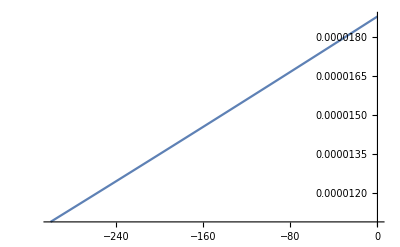

{voltage→-647.767}

{voltage→-415.099}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{voltage→-2.92425×10^6}

{voltage→-47.6096}

34.4716

2.5336

155617.

22.0899

```mathematica
(* this seems too complicated and for large Voc it does not reproduce the actual dynamic resistance because the I-V curve loses it's linearity *)
params = {doping->-2 10^22,thickness-> 13.5 10^-6,thickness6 -> 1 10^-6}
moleFrac10 = x/.FindRoot[Egfun[x,193/300 Tcell]==2 Pi hbar clight 10^6/echarge/10.6/.constants,{x,0.25}];
ISC10micron=18.791306240483216;
ISC6micron = 3.66;
Plot[10^-6 ISC10micron +10^-8 jAugRogalski[193/300 Tcell,moleFrac10,thickness,doping,voltage/10^6]+ 10^-8 jSRH[193/300 Tcell,10^-6,moleFrac10,thickness, doping,voltage/10^6]/.params/.constants,{voltage,-300,0}]
Voc10micron193K = FindRoot[10^-6 ISC10micron Exp[voltage 10^-6/(193 Tcell/300)]+10^-8 jAugRogalski[193/300 Tcell,moleFrac10,thickness,doping,voltage/10^6]+ 10^-8 jSRH[193/300 Tcell,0.5 10^-6,moleFrac10,thickness, doping,voltage/10^6]/.params/.constants,{voltage,-300,0}]
Voc6micron293K = FindRoot[10^-6 ISC6micron+10^-8 jAugRogalski[293/300 Tcell,moleFracCd,thickness6,doping,voltage/10^6]+ 10^-8 jSRH[293/300 Tcell, 10^-6,moleFrac10,thickness, doping,voltage/10^6]/.params/.constants,{voltage,-100,0}]
Voc6micron193K = FindRoot[10^-6 ISC6micron +10^-8 jAugRogalski[193/300 Tcell,moleFracCd,thickness6,doping,voltage/10^6]+ 10^-8 jSRH[193/300 Tcell, 10^-6,moleFrac10,thickness6, doping,voltage/10^6]/.params/.constants,{voltage,-300,0}]
Voc10micron293K = FindRoot[10^-6 ISC10micron +10^-8 jAugRogalski[293/300 Tcell,moleFrac10,thickness,doping,voltage/10^6]+ 10^-8 jSRH[293/300 Tcell,0.5 10^-6,moleFrac10,thickness6, doping,voltage/10^6]/.params/.constants,{voltage,-100,0}]
dynRes193 = -voltage/ISC10micron/.Voc10micron193K[[1]] (* should be 36 *)
dynRes293 = -voltage/ISC10micron/.Voc10micron293K[[1]]
dynRes6193 = -voltage/ISC10micron/.Voc6micron193K[[1]] (* should be 2.2 *)
dynRes6293 = -voltage/ISC10micron/.Voc6micron293K[[1]] (* should be 56 *)
```

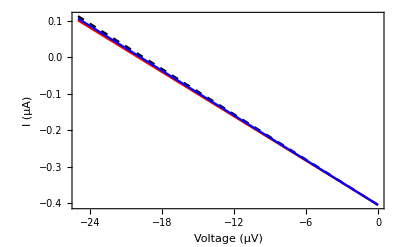

```mathematica
(* finding optimum p-doping *)
Plot[{10^6 current6p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,3 10^22]/.constants,10^6 current6p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,4 10^22]/.constants,
10^6 current6p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,5 10^22]/.constants},{voltage,-25,0},PlotStyle->{{Black,Dashed},Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (μA)",""},{"Voltage (μV)",""}},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
x/.FindRoot[Egfun[x,Tcell]==2 Pi hbar clight 10^6/echarge/5/.constants,{x,0.2}]
x/.FindRoot[Egfun[x,Tcell]==2 Pi hbar clight 10^6/echarge/4/.constants,{x,0.2}]
```

0.268309

0.314252

```mathematica
emittedLight5[T_,mu_] :=2.59407/2 0.9486423778113563 (* this needs to be recalculated with the eqe of the 5 micron diode *) emittedLight5planar[T,mu] nLens^2 0.45545957976535084(* see calculation of escape probability above *) 10^-8 (* area of diode *);
(emittedLight5[293Tcell/300/.constants,0]-emittedLight5[286 Tcell/300/.constants,0])
emittedLight4[T_,mu_] :=2.59407/2 0.9486423778113563 (* this needs to be recalculated with the eqe of the 5 micron diode *) emittedLight4planar[T,mu] nLens^2 0.45545957976535084(* see calculation of escape probability above *) 10^-8 (* area of diode *);
(emittedLight4[293Tcell/300/.constants,0]-emittedLight4[286 Tcell/300/.constants,0])
current5p[Tdiode_,Tenv_,voltage_,thickness_,tauSRH_,pdope_] := -emittedLight5[Tdiode,voltage]+emittedLight5[Tenv,0]-10^-8(* actual active area of the device *)jSRH[Tdiode,tauSRH,0.27,thickness,-pdope,voltage]-10^-8 jAugRogalski[Tdiode,0.27,thickness,-pdope,voltage]; 
current4p[Tdiode_,Tenv_,voltage_,thickness_,tauSRH_,pdope_] := -emittedLight4[Tdiode,voltage]+emittedLight4[Tenv,0]-10^-8(* actual active area of the device *)jSRH[Tdiode,tauSRH,0.315,thickness,-pdope,voltage]-10^-8 jAugRogalski[Tdiode,0.315,thickness,-pdope,voltage];
```

1.60784×10^-7

5.18271×10^-8

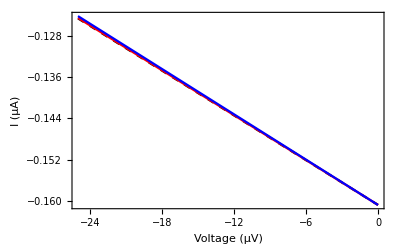

```mathematica
(* finding optimum p-doping *)
Plot[{10^6 current5p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,3 10^22]/.constants,10^6 current5p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,2.5 10^22]/.constants,
10^6 current5p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,3.5 10^22]/.constants},{voltage,-25,0},PlotStyle->{{Black,Dashed},Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (μA)",""},{"Voltage (μV)",""}},PerformanceGoal->"Speed",PlotRange->All]
```

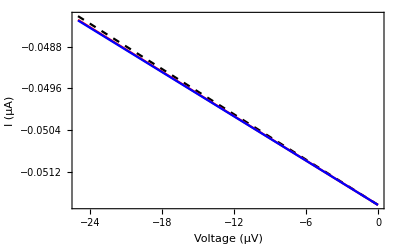

```mathematica
(* finding optimum p-doping *)
Plot[{10^6 current4p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,3 10^22]/.constants,10^6 current4p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6, 3.5 10^22]/.constants,
10^6 current4p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,4 10^22]/.constants},{voltage,-25,0},PlotStyle->{{Black,Dashed},Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (μA)",""},{"Voltage (μV)",""}},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
res5p =10/Abs[10^6 (current5p[293Tcell/300/.constants,3 Tcell/300/.constants,10/10^6,18 10^-6,10^-6,3 10^22]-current5p[293Tcell/300/.constants,3 Tcell/300/.constants,0,18 10^-6,10^-6,3 10^22])]/.constants
res4p =10/Abs[10^6 (current4p[293Tcell/300/.constants,286 Tcell/300/.constants,10/10^6,15 10^-6,10^-6,3 10^22]-current4p[293Tcell/300/.constants,286 Tcell/300/.constants,0,15 10^-6,10^-6,3 10^22])]/.constants
```

387.181

4698.36

## Analyse Fan’s separation of the dynamic resistance into series and shunt resistance (eq. (5) of Santhanam)

I (V) = q Φ_em (V-I R_s)-q Φ_abs+(V-I R_s)/R_sh

Fan only measures the short circuit current, so it is sufficient to understand the impact on the short circuit current to understand whether they can get that information.

I_sc(1+R_s/R_sh+(qΦ_em(0)R_s)/(k T))=q(Φ_em(0)-Φ_abs) with Φ_em,Φ_abs∼A_opt

I do not see how this allows separation of R_s and R_shwithout independent knowledge of A_opt or information on the voltage dependence of the current

Nonradiative recombination could be written as shunt resistance, however, as long as we stay in the low-voltage regime.

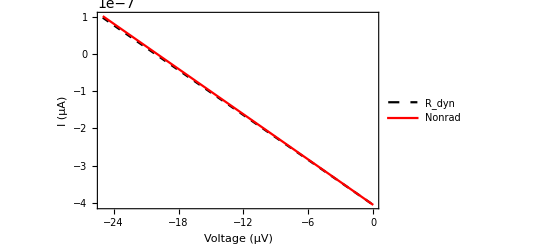

```mathematica
Plot[{current6p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,0,10^-6,3 10^22]-voltage/10^6/50/.constants,current6p[293Tcell/300/.constants,286 Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,4 10^22]/.constants},{voltage,-25,0},PerformanceGoal->"Speed",PlotStyle->{{Black,Dashed},Red},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"I (μA)",""},{"Voltage (μV)",""}},PlotRange->All,PlotLegends->Placed[LineLegend[{"R_dyn","Nonrad"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.75,0.75}]]
```

## Fitting EL data to obtain series and shunt resistance

Rdyn = Rs + (J0,nr/(kT)+J0,rad/(kT)+1/Rsh)^-1

dark for ideality factor 1 recombination: I(mu)=I0,rad (Exp[mu/(kT)]− 1) + I0,nr (Exp[mu/(kT)]-1) + mu/Rsh

mu = V + I Rs

ϕ_(EL,norm)=Exp[mu/(kT)]-1

mu(V) = kT Log[ϕ_(EL,norm)+1]

I-V close to zero: I(V)=Isc_rad + (V-I*Rs)*(J0/(kT) + 1/Rsh) -> I(0) = Isc_rad/(1-Rs*(J0/(kT)+1/Rsh))=Isc_rad/(1+Rs/(Rdyn-Rs))=Isc_rad*(Rdyn-Rs)/Rdyn

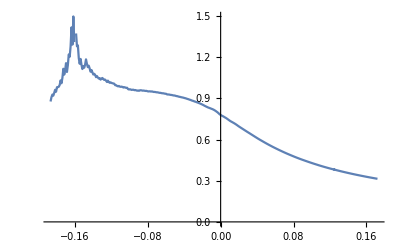

```mathematica
muV6 = Table[0,Length[el6V]];
For[i=1,i≤ Length[el6V],i++,
muV6[[i]] = Re[UnitStep[el6V[[i]]]Tcell 293/300 Log[el6S[[i]]+1]+UnitStep[-el6V[[i]]] Tcell 293/300 Log[1-el6S[[i]]]]/.constants
]
muNorm = muV6/el6V;
ListPlot[Transpose[{el6V,muNorm}],Joined->True]
```

```mathematica
emittedLight6[293Tcell/300/.constants,0]
```

1.96937×10^-6

```mathematica
elIVmu[mu_,thickness_,Rsh_] := 10^-8(* actual active area of the device *)jSRH[293 Tcell/300,10^-6,moleFracCd,thickness,-4 10^22,mu]+10^-8 jAugRogalski[293 Tcell/300,moleFracCd,thickness,-4 10^22,mu]+ 1.97 10^-6(Exp[300 (mu)/293/Tcell]-1)+mu/Rsh;
(*elIV[V_,current_,Rs_,thickness_] := 10^-8(* actual active area of the device *)jSRH[293 Tcell/300,10^-6,moleFracCd,thickness,-4 10^22,V+current Rs]-10^-8 jAugRogalski[293 Tcell/300,moleFracCd,thickness,-4 10^22,V+current Rs]+ 1.97 10^-6(Exp[300 (V+current Rs)/293/Tcell]-1);*)
```

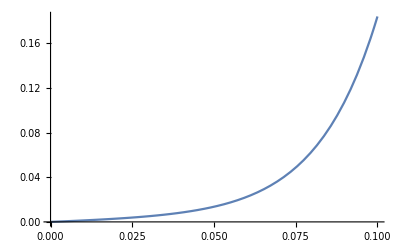

```mathematica
Plot[elIVmu[mu,10^-5,10]/.constants,{mu,0,0.1}]
```

```mathematica
VfromMu[mu_,thickness_,Rsh_,Rs_] := mu+elIVmu[mu,thickness,Rsh] Rs/.constants;
```

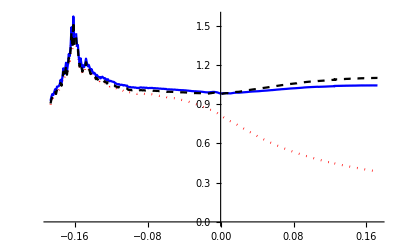

```mathematica
ListPlot[{Transpose[{el6V,VfromMu[muV6,10 10^-6,50,1]/el6V}],Transpose[{el6V,VfromMu[muV6,10 10^-6,300,11]/el6V}],Transpose[{el6V,VfromMu[muV6,10 10^-6,1000,12]/el6V}]},Joined->True,PlotStyle->{{Red,Dotted},Blue,{Black,Dashed}}]
```

```mathematica
Rdyn[Rs_,Rsh_,thickness_]:= Rs+(1/Rsh+10^-8(j0SRH[293 Tcell/300,10^-6,moleFracCd,thickness,-4 10^22]+j0Aug[293 Tcell/300,moleFracCd,thickness,-4 10^22])300/293/ Tcell)^-1/.constants;
```

```mathematica
Rdyn[12,400,10 10^-6]
```

56.0828

```mathematica
Solve[current == I0rad(Exp[(V+current Rs)/T]-1)+(V+ current Rs)/Rsh(*+I0nr (Exp[3/2(V+current Rs)/T]-Exp[1/2(V+current Rs)/T])*),current]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{current→(I0rad Rs Rsh-Rs V-Rs T ProductLog[(ⅇ^((I0rad Rs Rsh)/((Rs-Rsh) T)+V/T-(Rs V)/((Rs-Rsh) T)) I0rad Rs Rsh)/((Rs-Rsh) T)]+Rsh T ProductLog[(ⅇ^((I0rad Rs Rsh)/((Rs-Rsh) T)+V/T-(Rs V)/((Rs-Rsh) T)) I0rad Rs Rsh)/((Rs-Rsh) T)])/(Rs (Rs-Rsh))}}

## Power generation

```mathematica
temps = Table[i,{i,280,310}];
openCircuitVoltages = Table[0,Length[temps]];
For[i=1,i≤Length[temps],i++,
openCircuitVoltages[[i]]=FindRoot[current6p[293Tcell/300/.constants,temps[[i]] Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,4 10^22]/.constants,{voltage,3(i-293)}];
]
powerDiffTemps = Table[10^6 current6p[293 Tcell/300/.constants,temps[[i]]Tcell/300,0,10 10^-6,10^-6,4 10^22]voltage /4/.openCircuitVoltages[[i]]/.constants,{i,1,Length[temps]}];(*units of pW*)
```

NIntegrate::inumr: The integrand («1»)/(-1+ⅇ^(39.6059 (energy-voltage/1000000))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.17393,0.175541}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
openCircuitVoltages=FindRoot[current6p[293Tcell/300/.constants,280  Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,4 10^22]/.constants,{voltage,3(280-293)}];
```

NIntegrate::inumr: The integrand («1»)/(-1+ⅇ^(39.6059 (energy-voltage/1000000))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.17393,0.175541}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
openCircuitVoltages
```

{voltage→-34.3766}

```mathematica
0.403989109901363/1.97
```

0.205071

```mathematica
oC=FindRoot[current6p[293Tcell/300/.constants,3Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,4 10^22]/.constants,{voltage,3(280-293)}]
```

NIntegrate::inumr: The integrand («1»)/(-1+ⅇ^(39.6059 (energy-voltage/1000000))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.17393,0.175541}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{voltage→-97.5386}

```mathematica
powerDiffTemp3K = 10^6 current6p[293 Tcell/300/.constants,3 Tcell /300 /.constants,0,10 10^-6,10^-6,4 10^22]voltage /4/.oC/.constants
```

48.0224

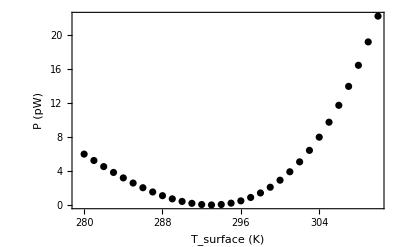

```mathematica
ListPlot[Transpose[{temps,powerDiffTemps}],PlotStyle->{{Black}},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"P (pW)",""},{"T_surface (K)","T_TRD=273 K"}}]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Dropbox","Thermoradiative diode","Calculations","powergen6micron.csv"}],{temps,powerDiffTemps}]
```

/Users/andreaspusch/Dropbox/Thermoradiative diode/Calculations/powergen6micron.csv

```mathematica
tempsSurface = Table[i,{i,280,310}];
tempsDiode = Table[i,{i,293,294.6,0.2}];
VocVaryingDiodeT = Table[0,Length[tempsSurface]Length[tempsDiode]];
For[i=1,i≤Length[tempsSurface],i++,
For[j=1,j≤ Length[tempsDiode],j++,
VocVaryingDiodeT[[i+(j-1) Length[tempsSurface]]]=FindRoot[current6p[tempsDiode[[j]] Tcell/300/.constants,tempsSurface[[i]] Tcell/300/.constants,voltage/10^6,10 10^-6,10^-6,4 10^22]/.constants,{voltage,3(tempsSurface[[i]]-tempsDiode[[j]])}];
]
]
powerDiffTempsDiode = Table[10^6 current6p[tempsDiode[[Ceiling[k/Length[tempsSurface]]]] Tcell/300/.constants,tempsSurface[[Mod[k,Length[tempsSurface]]+1]]Tcell/300,0,10 10^-6,10^-6,4 10^22]voltage /4/.VocVaryingDiodeT[[k]]/.constants,{k,1,Length[tempsDiode]Length[tempsSurface]}];(*units of pW*)
```

NIntegrate::inumr: The integrand («1»)/(-1+ⅇ^(39.6059 (energy-voltage/1000000))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.17393,0.175541}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
tempsDiode[[Mod[4,Length[tempsSurface]]]]
```

List

```mathematica
powerDiffTempsDiode
```

{5.59106,4.85503,4.15206,3.48635,2.86235,2.28476,1.75861,1.28916,0.88203,0.543128,0.278702,0.0953419,-2.28848×10^-15,4.19877×10^-17,0.103054,0.317279,0.651209,1.11382,1.71452,2.46322,3.3703,4.44662,5.70362,7.15323,8.80797,10.6809,12.7858,15.137,17.7493,20.6385,-11.5022,5.77234,5.02607,4.31228,3.63512,2.99901,2.40863,1.86896,1.38523,0.963012,0.608178,0.326931,0.125817,0.011738,-0.00803063,0.0741712,0.266405,0.57715,1.01532,1.59027,2.31184,3.19033,4.23656,5.46187,6.87812,8.49777,10.3338,12.3999,14.7102,17.2796,20.1237,-11.5376,5.95654,5.20009,4.47554,3.78699,3.13885,2.53575,1.98264,1.48471,1.04749,0.676822,0.378852,0.160087,0.0273803,-0.0120418,0.049429,0.219801,0.507495,0.921367,1.47071,2.1653,3.01538,4.03169,5.22549,6.60859,8.19335,9.99268,12.0201,14.2898,16.8166,19.6158,-11.5689,6.14366,5.37709,4.64183,3.94197,3.28187,2.66613,2.09965,1.5876,1.13548,0.749058,0.434463,0.198149,0.0469234,-0.0120378,0.0288229,0.177459,0.442238,0.831955,1.35585,2.02362,2.84544,3.832,4.99449,6.34463,7.89469,9.65753,11.6466,13.8759,16.3602,19.1149,-11.596,6.3337,5.55708,4.81118,4.10006,3.42806,2.79975,2.21999,1.69391,1.22696,0.824884,0.493761,0.240001,0.0703638,-0.00802249,0.0123481,0.139376,0.381373,0.747075,1.24566,1.88677,2.68051,3.6375,4.76885,6.08621,7.60178,9.32834,11.2792,13.4685,15.9106,18.6209,-11.619,6.52667,5.74004,4.98356,4.26126,3.57744,2.93663,2.34366,1.80363,1.32194,0.904299,0.556744,0.285639,0.0976982,1.81583×10^-13,-3.38065×10^-17,0.105546,0.324893,0.666721,1.14015,1.75475,2.52057,3.44815,4.54855,5.83333,7.31462,9.00511,10.9181,13.0674,15.4676,18.1338,-11.6378,6.72256,5.92599,5.15899,4.42558,3.72999,3.07676,2.47066,1.91675,1.42041,0.987301,0.62341,0.335061,0.128923,0.0120257,-0.00822605,0.0759629,0.272793,0.590886,1.0393,1.62755,2.36561,3.26397,4.33359,5.58597,7.03318,8.68781,10.5631,12.6727,15.0312,17.6536,-11.6525,6.92139,6.11493,5.33747,4.593,3.88573,3.22014,2.60098,2.03329,1.52238,1.07389,0.693757,0.388265,0.164036,0.0280508,-0.0123346,0.0506219,0.225066,0.519563,0.94311,1.50516,2.21563,3.08492,4.12395,5.34413,6.75745,8.37643,10.2142,12.2844,14.6015,17.1803,-11.663,7.12314,6.30685,5.519,4.76354,4.04465,3.36678,2.73464,2.15324,1.62785,1.16406,0.767782,0.445247,0.203032,0.0480715,-0.0123302,0.0295179,0.181707,0.452745,0.851571,1.38757,2.07061,2.91101,3.91962,5.10779,6.48742,8.07096,9.87143,11.9025,14.1783,16.7138,-11.6694}

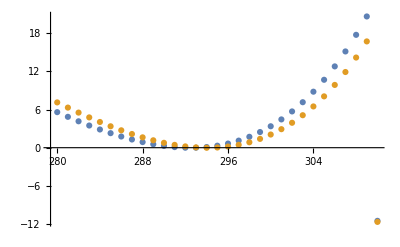

```mathematica
ListPlot[{Transpose[{tempsSurface,powerDiffTempsDiode[[1;;Length[tempsSurface]]]}],Transpose[{tempsSurface,powerDiffTempsDiode[[(Length[tempsDiode]-1)Length[tempsSurface]+1;;Length[tempsDiode]Length[tempsSurface]]]}]}]
```

EQEmeasured /0.714 = EQEinternal 
1 - Exp[-absCoeff d] = EQEinternal -> EQEinternal - 1 = -Exp[-absCoeff d] -> x := absCoeff d = -Log[1 - EQEinternal] 
EQEbeta = 1 - Exp[-absCoeff d/Cos[beta]] -> EQEbeta = 1 - Exp[Log[1 - EQEinternal]/Cos[beta]] = 1 - Exp[Log[1 - EQEmeasured/0.714]/Cos[beta]]

## Absorption coefficient of HgCdTe (Jaksic1995 “Simple Approximation for Absorption Coefficient of Degenerate HgCdTe”)

```mathematica
(* Absorption coefficient *)
alphaHgCdTe[x_,T_,om_] = (1480 x +0.26 T 300/Tcell +90)Exp[3.915(om-Egfun[x,T])^(1/3)](Tanh[120 Tanh[10 x -1.5](om-Egfun[x,T])]+1);
```

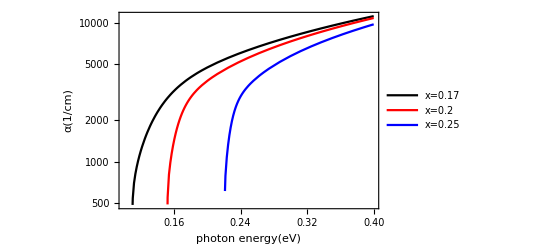

```mathematica
LogPlot[{alphaHgCdTe[0.17,293/300 Tcell,om]/.constants,alphaHgCdTe[0.2,293/300 Tcell,om]/.constants,alphaHgCdTe[0.25,293/300 Tcell,om]/.constants},{om,0.1,0.4},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"α(1/cm)",""},{"photon energy(eV)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"x=0.17","x=0.2","x=0.25"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.75,0.25}]]
```

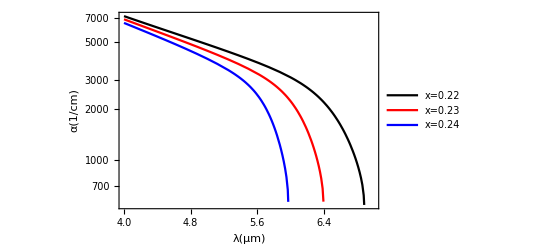

```mathematica
LogPlot[{alphaHgCdTe[0.22,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]/.constants,alphaHgCdTe[0.23,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]/.constants,alphaHgCdTe[0.24,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]/.constants},{lambda,4,7},PlotStyle->{Black,Red,Blue},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"α(1/cm)",""},{"λ(μm)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"x=0.22","x=0.23","x=0.24"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.25,0.25}]]
```

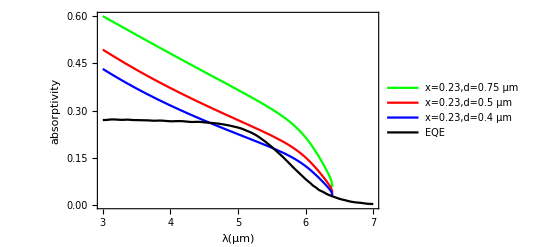

```mathematica
Plot[{0.75 (1-Exp[-alphaHgCdTe[0.23,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]1.5 10^-4])/.constants,0.75 (1-Exp[-alphaHgCdTe[0.23,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge] 10^-4])/.constants,0.75(1-Exp[-alphaHgCdTe[0.23,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]8 10^-5])/.constants,eqeFun[2 Pi hbar clight/10^-6/lambda/echarge/.constants]},{lambda,3,7},PlotStyle->{Green,Red,Blue,Black},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"absorptivity",""},{"λ(μm)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"x=0.23,d=0.75 μm","x=0.23,d=0.5 μm","x=0.23,d=0.4 μm","EQE"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.8,0.7}]]
```

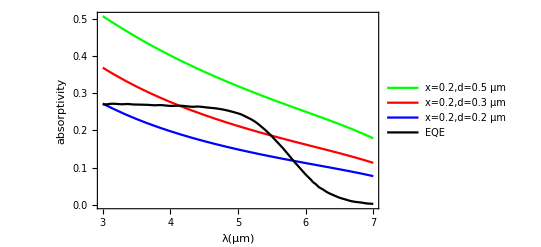

```mathematica
Plot[{0.75 (1-Exp[-alphaHgCdTe[0.2,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]1 10^-4])/.constants,0.75 (1-Exp[-alphaHgCdTe[0.2,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]0.6 10^-4])/.constants,0.75(1-Exp[-alphaHgCdTe[0.2,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge] 4 10^-5])/.constants,eqeFun[2 Pi hbar clight/10^-6/lambda/echarge/.constants]},{lambda,3,7},PlotStyle->{Green,Red,Blue,Black},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"absorptivity",""},{"λ(μm)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"x=0.2,d=0.5 μm","x=0.2,d=0.3 μm","x=0.2,d=0.2 μm","EQE"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.8,0.7}]]
```

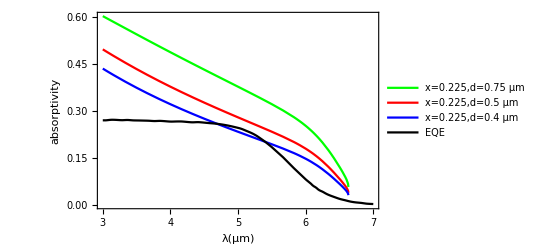

```mathematica
Plot[{0.75 (1-Exp[-alphaHgCdTe[0.225,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]1.5 10^-4])/.constants,0.75 (1-Exp[-alphaHgCdTe[0.225,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge] 10^-4])/.constants,0.75(1-Exp[-alphaHgCdTe[0.225,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]8 10^-5])/.constants,eqeFun[2 Pi hbar clight/10^-6/lambda/echarge/.constants]},{lambda,3,7},PlotStyle->{Green,Red,Blue,Black},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"absorptivity",""},{"λ(μm)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"x=0.225,d=0.75 μm","x=0.225,d=0.5 μm","x=0.225,d=0.4 μm","EQE"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.8,0.7}]]
```

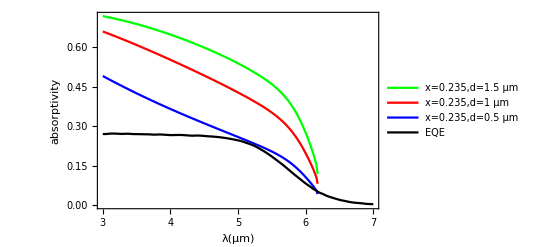

```mathematica
Plot[{0.75 (1-Exp[-alphaHgCdTe[0.235,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge] 3 10^-4])/.constants,0.75 (1-Exp[-alphaHgCdTe[0.235,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge] 2 10^-4])/.constants,0.75(1-Exp[-alphaHgCdTe[0.235,293/300 Tcell,2 Pi hbar clight/10^-6/lambda/echarge]1 10^-4])/.constants,eqeFun[2 Pi hbar clight/10^-6/lambda/echarge/.constants]},{lambda,3,7},PlotStyle->{Green,Red,Blue,Black},Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14,Black},FrameLabel->{{"absorptivity",""},{"λ(μm)",""}},PerformanceGoal->"Speed",PlotLegends->Placed[LineLegend[{"x=0.235,d=1.5 μm","x=0.235,d=1 μm","x=0.235,d=0.5 μm","EQE"},LabelStyle->{GrayLevel[0.1],11},LegendLayout->{"Row",4}],{0.8,0.7}]]
```